# Schwinger Integrand in Holomorphic - Topological Field Theories

This notebook contains the Mathematica code associated with the paper https://arxiv.org/abs/2403.13049

To utilize this notebook, it is essential to first load the accompanying Mathematica package. 
Please ensure to execute Get[“omegabook.m”] at the beginning of your session.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["omegabook.m"]
```

Success! Welcome to Holomorphic Twist

## Example

### Example : Laman

#### Example : 1 -> 2 topological

```mathematica
graph = Graph[{1->2}];
%//print
```

-Graphics-

```mathematica
xvars[graph]
dxvars[graph]
tvars[graph]
dtvars[graph]
```

{x[1],x[2]}

{dif[x[1]],dif[x[2]]}

{t[1->2]}

{dif[t[1->2]]}

```mathematica
svars[graph]
```

{-x[1]/(√t[1->2])+x[2]/(√t[1->2])}

```mathematica
smeasure[graph]
stmeasure[graph]
```

-dif[x[1]]/(√t[1->2])+(dif[t[1->2]] x[1])/(2 t[1->2]^(3/2))

-1/(√t[1->2])

```mathematica
sexp[graph]//Expand
sA[graph]
```

x[1]^2/t[1->2]-(2 x[1] x[2])/t[1->2]+x[2]^2/t[1->2]

{{2/t[1->2]}}

```mathematica
somega[graph]
```

-√π

#### Example : 1 -> 2 holomorphic

```mathematica
graph = Graph[{1->2}];
%//print
```

-Graphics-

```mathematica
zvars[graph]
zbvars[graph]
tvars[graph]
```

{z[1],z[2]}

{zb[1],zb[2]}

{t[1->2]}

```mathematica
xyexp[graph]
```

(-z[1]+z[2]) (-zb[1]/t[1->2]+zb[2]/t[1->2])+(-zb[1]/t[1->2]+zb[2]/t[1->2]) δ[1->2]

```mathematica
yvars[graph]
```

{-zb[1]/t[1->2]+zb[2]/t[1->2]}

```mathematica
ytmeasure[graph]
```

-ⅇ^(z[1] λ[1])/t[1->2]

```mathematica
xyomega[graph]//printBeauty
```

-ⅇ^(z[1] λ[1]) π

```mathematica
rho = xyomega[graph]/.{ⅇ^(z[1] λ[1]+z[2] λ[2])->1}//FullSimplify[#,t[1->2]>0]&
```

-ⅇ^(z[1] λ[1]) π

#### Example : 1 -> 2, 2 -> 3, 3 -> 1 holomorphic

```mathematica
graph = Graph[{1->2,2->3,3->1}];
graph//print
```

-Graphics-

```mathematica
zvars[graph]
zbvars[graph]
tvars[graph]
```

{z[1],z[2],z[3]}

{zb[1],zb[2],zb[3]}

{t[1->2],t[2->3],t[3->1]}

```mathematica
xyexp[graph]
```

(-z[1]+z[2]) (-zb[1]/t[1->2]+zb[2]/t[1->2])+(-z[2]+z[3]) (-zb[2]/t[2->3]+zb[3]/t[2->3])+(z[1]-z[3]) (zb[1]/t[3->1]-zb[3]/t[3->1])+(-zb[1]/t[1->2]+zb[2]/t[1->2]) δ[1->2]+(-zb[2]/t[2->3]+zb[3]/t[2->3]) δ[2->3]+(zb[1]/t[3->1]-zb[3]/t[3->1]) δ[3->1]

```mathematica
yvars[graph]
```

{-zb[1]/t[1->2]+zb[2]/t[1->2],-zb[2]/t[2->3]+zb[3]/t[2->3],zb[1]/t[3->1]-zb[3]/t[3->1]}

```mathematica
ytmeasure[graph]//printBeauty
```

(ⅇ^(z[1] λ[1]+z[2] λ[2]) (-dif[t_31] t_12 t_23 zb[1]+t_31 (dif[t_12] t_23 (zb[1]-zb[2])+dif[t_23] t_12 zb[2])))/(t_12^2 t_23^2 t_31^2)

```mathematica
rho = xyomega[graph]/.{ⅇ^(z[1] λ[1]+z[2] λ[2])->1}//printBeauty
```

(π^2 (dif[t_12] (t_31 λ[1]-t_23 λ[2])-dif[t_31] (t_12 λ[1]+t_23 (λ[1]+λ[2]))+dif[t_23] (t_12 λ[2]+t_31 (λ[1]+λ[2]))))/(t_12+t_23+t_31)^2

```mathematica
Exp[-Drop[λvars[graph],-1].ixyA[graph].xδB[graph].δvars[graph]]//printBeauty
```

ⅇ^(((t_31 (δ[1->2]+δ[2->3])-(t_12+t_23) δ[3->1]) λ[1]+((t_12+t_31) δ[2->3]-t_23 (δ[1->2]+δ[3->1])) λ[2])/(t_12+t_23+t_31))

#### Example : 1 -> 2, 2 -> 3, 3 -> 1 top

```mathematica
graph = Graph[{1->2,2->3,3->1}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,True,False,False,False,False}

```mathematica
sA[graph]//Simplify//MatrixForm
(* sAfromAM[graph]/.t[edge_]:>t[Position[EdgeList[graph],edge][[1,1]]] //MatrixForm*)
```

(2 (1/t[1->2]+1/t[3->1]) | -2/t[1->2]
-2/t[1->2] | 2 (1/t[1->2]+1/t[2->3]))

```mathematica
temp = somega[graph]//Collect[#,dif[__],Simplify]&
```

0

```mathematica
wedge[temp,temp]//Simplify
```

0

#### Example : 1 -> 2, 2 -> 3, 3 -> 1 top

```mathematica
graph = Graph[{1->2,2->3,3->1,3->4}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,False,False}

```mathematica
sA[graph]//Simplify//MatrixForm
```

(2 (1/t[1->2]+1/t[3->1]) | -2/t[1->2] | -2/t[3->1]
-2/t[1->2] | 2 (1/t[1->2]+1/t[2->3]) | -2/t[2->3]
-2/t[3->1] | -2/t[2->3] | 2 (1/t[2->3]+1/t[3->1]+1/t[3->4]))

```mathematica
temp= somega[graph]//Collect[#,dif[__],Simplify]&
```

0

```mathematica
wedge[temp,temp]//Simplify
```

0

#### Example : 1 -> 2, 2 -> 3, 3 -> 1, 2 -> 4, 4 -> 3 top

```mathematica
graph = Graph[{1->2,2->3,3->1,2->4,4->3}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,True,False,False,False,False}

```mathematica
sA[graph]/.changeEdgeLabel[graph]//MatrixForm
```

(2/t[1->2]+2/t[3->1] | -2/t[1->2] | -2/t[3->1]
-2/t[1->2] | 2/t[1->2]+2/t[2->3]+2/t[2->4] | -2/t[2->3]
-2/t[3->1] | -2/t[2->3] | 2/t[2->3]+2/t[3->1]+2/t[4->3])

```mathematica
αtop =somega[graph]//Collect[#,dif[__],Simplify]&;(*//printBeauty*)
```

```mathematica
αtop==π^(3/2)/8(Subscript[t, 31] (Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 12] (Subscript[t, 23]+Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 23] (Subscript[t, 24]+Subscript[t, 31]+Subscript[t, 43]))^(-3/2)(dif[Subscript[t, 23],Subscript[t, 24]] Subscript[t, 12]+dif[Subscript[t, 23],Subscript[t, 43]] Subscript[t, 12]-dif[Subscript[t, 12],Subscript[t, 24]] Subscript[t, 23]-dif[Subscript[t, 12],Subscript[t, 43]] Subscript[t, 23]+dif[Subscript[t, 24],Subscript[t, 31]] Subscript[t, 23]-dif[Subscript[t, 31],Subscript[t, 43]] Subscript[t, 23]+dif[Subscript[t, 12],Subscript[t, 23]] Subscript[t, 24]-dif[Subscript[t, 23],Subscript[t, 31]] Subscript[t, 24]+dif[Subscript[t, 23],Subscript[t, 24]] Subscript[t, 31]+dif[Subscript[t, 23],Subscript[t, 43]] Subscript[t, 31]+dif[Subscript[t, 12],Subscript[t, 23]] Subscript[t, 43]-dif[Subscript[t, 23],Subscript[t, 31]] Subscript[t, 43])//printBeauty//FullSimplify
```

True

```mathematica
wedge[αtop,αtop]//Simplify
```

0

```mathematica
ρhol = xyomega[graph]/.ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3])->1//Simplify
```

```mathematica
omegaholtop =wedge[αtop,ρhol]//printBeauty
```

(π^(9/2) (dif[t_23,t_24,t_31,t_43] t_12-dif[t_12,t_24,t_31,t_43] t_23+dif[t_12,t_23,t_31,t_43] t_24-dif[t_12,t_23,t_24,t_43] t_31+dif[t_12,t_23,t_24,t_31] t_43) λ[1] (λ[1]+λ[2]+λ[3]))/(4 (t_31 (t_24+t_43)+t_12 (t_23+t_24+t_43)+t_23 (t_24+t_31+t_43))^(5/2))

```mathematica
omegaholtop/(-1/4 π^2 dtttt[{Subscript[t, 12],Subscript[t, 23],Subscript[t, 24],Subscript[t, 31],Subscript[t, 43]}]  Subscript[t, 12] Subscript[t, 23] Subscript[t, 24] Subscript[t, 31] Subscript[t, 43] (Subscript[t, 31] (Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 12] (Subscript[t, 23]+Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 23] (Subscript[t, 24]+Subscript[t, 31]+Subscript[t, 43]))^(-5/2))//Simplify
```

π^(5/2) λ[1] (λ[1]+λ[2]+λ[3])

```mathematica
dtttt[{Subscript[t, 12],Subscript[t, 23],Subscript[t, 24],Subscript[t, 31],Subscript[t, 43]}]
```

-dif[t_12,t_23,t_24,t_31]/(t_12 t_23 t_24 t_31)+dif[t_12,t_23,t_24,t_43]/(t_12 t_23 t_24 t_43)-dif[t_12,t_23,t_31,t_43]/(t_12 t_23 t_31 t_43)+dif[t_12,t_24,t_31,t_43]/(t_12 t_24 t_31 t_43)-dif[t_23,t_24,t_31,t_43]/(t_23 t_24 t_31 t_43)

```mathematica
λvars[graph][[1;;3]].ixyA[graph].xδB[graph].zevars[graph]//printBeauty
```

(t_43 (t_12 (ze_31 λ[1]+ze_23 (λ[1]+λ[3])-ze_24 (λ[1]+λ[2]+λ[3]))-t_31 (ze_12 λ[1]-ze_23 λ[3]+ze_24 (λ[1]+λ[2]+λ[3])))+t_23 (t_12 ze_31 λ[1]+t_24 ze_31 λ[1]+t_12 ze_43 λ[1]+t_24 ze_43 λ[1]+t_24 ze_12 λ[2]-t_12 ze_24 λ[2]+t_24 ze_31 λ[2]+t_24 ze_43 λ[2]+(t_12+t_24) ze_43 λ[3]-t_31 (ze_12 λ[1]+ze_24 (λ[1]+λ[2])-ze_43 λ[3])-t_43 (ze_31 λ[3]+ze_12 (λ[1]+λ[3])+ze_24 (λ[1]+λ[2]+λ[3])))+t_24 (t_12 (ze_31 λ[1]-ze_23 λ[2]+ze_43 (λ[1]+λ[2]+λ[3]))+t_31 (-ze_12 λ[1]-ze_23 (λ[1]+λ[2])+ze_43 (λ[1]+λ[2]+λ[3]))))/(t_31 (t_24+t_43)+t_12 (t_23+t_24+t_43)+t_23 (t_24+t_31+t_43))

```mathematica
temp = (Subscript[t, 23] (Subscript[t, 12] Subscript[ze, 31] λ[1]+Subscript[t, 24] Subscript[ze, 31] λ[1]+Subscript[t, 12] Subscript[ze, 43] λ[1]+Subscript[t, 24] Subscript[ze, 43] λ[1]+Subscript[t, 24] Subscript[ze, 12] λ[2]-Subscript[t, 12] Subscript[ze, 24] λ[2]+Subscript[t, 24] Subscript[ze, 31] λ[2]+Subscript[t, 24] Subscript[ze, 43] λ[2]+(Subscript[t, 12]+Subscript[t, 24]) Subscript[ze, 43] λ[3]-Subscript[t, 31] (Subscript[ze, 12] λ[1]+Subscript[ze, 24] (λ[1]+λ[2])-Subscript[ze, 43] λ[3])-Subscript[t, 43] (Subscript[ze, 31] λ[3]+Subscript[ze, 12] (λ[1]+λ[3])-Subscript[ze, 24] λ[4]))+Subscript[t, 43] (-Subscript[t, 31] (Subscript[ze, 12] λ[1]-Subscript[ze, 23] λ[3]-Subscript[ze, 24] λ[4])+Subscript[t, 12] (Subscript[ze, 31] λ[1]+Subscript[ze, 23] (λ[1]+λ[3])+Subscript[ze, 24] λ[4]))+Subscript[t, 24] (Subscript[t, 12] (Subscript[ze, 31] λ[1]-Subscript[ze, 23] λ[2]-Subscript[ze, 43] λ[4])+Subscript[t, 31] (-Subscript[ze, 12] λ[1]-Subscript[ze, 23] (λ[1]+λ[2])-Subscript[ze, 43] λ[4])))/(Subscript[t, 31] (Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 12] (Subscript[t, 23]+Subscript[t, 24]+Subscript[t, 43])+Subscript[t, 23] (Subscript[t, 24]+Subscript[t, 31]+Subscript[t, 43]))//FullSimplify
```

(t_23 (t_12 ze_31 λ[1]+t_24 ze_31 λ[1]+t_12 ze_43 λ[1]+t_24 ze_43 λ[1]+t_24 ze_12 λ[2]-t_12 ze_24 λ[2]+t_24 ze_31 λ[2]+t_24 ze_43 λ[2]+(t_12+t_24) ze_43 λ[3]-t_31 (ze_12 λ[1]+ze_24 (λ[1]+λ[2])-ze_43 λ[3])-t_43 (ze_31 λ[3]+ze_12 (λ[1]+λ[3])-ze_24 λ[4]))+t_43 (t_31 (-ze_12 λ[1]+ze_23 λ[3]+ze_24 λ[4])+t_12 (ze_31 λ[1]+ze_23 (λ[1]+λ[3])+ze_24 λ[4]))-t_24 (t_12 (-ze_31 λ[1]+ze_23 λ[2]+ze_43 λ[4])+t_31 (ze_12 λ[1]+ze_23 (λ[1]+λ[2])+ze_43 λ[4])))/(t_31 (t_24+t_43)+t_12 (t_23+t_24+t_43)+t_23 (t_24+t_31+t_43))

```mathematica
xyA[graph]
```

{{1/t[1->2]+1/t[3->1],-1/t[1->2],-1/t[3->1]},{-1/t[1->2],1/t[1->2]+1/t[2->3]+1/t[2->4],-1/t[2->3]},{-1/t[3->1],-1/t[2->3],1/t[2->3]+1/t[3->1]+1/t[4->3]}}

```mathematica
xδB[graph].zevars[graph]//printBeauty
```

{-ze_12/t_12+ze_31/t_31,ze_12/t_12-ze_23/t_23-ze_24/t_24,ze_23/t_23-ze_31/t_31+ze_43/t_43}

```mathematica
Jac[A_,B_]:=Table[D[A[[i]],B[[j]]],{i,Length[A]},{j,Length[B]}]
Jac[{(*t[12],*) t[23]/t[12], t[24]/t[12], t[31]/t[12] ,t[43]/t[12]},{(*t[12],*) t[23], t[24], t[31] ,t[43]}]//Det
```

1/t[12]^4

```mathematica
dtmeasure = {(dt[2->3]dt[3->1]dt[2->4]dt[4->3])/(t[2->3] t[3->1] t[2->4] t[4->3]),-(dt[1->2]dt[3->1]dt[2->4]dt[4->3])/(t[1->2]   t[3->1]t[2->4] t[4->3]),(dt[1->2]dt[2->3]dt[2->4]dt[4->3])/(t[1->2] t[2->3] t[2->4]  t[4->3]),-(dt[1->2]dt[2->3]dt[3->1]dt[4->3])/(t[1->2] t[2->3] t[3->1] t[4->3]),(dt[1->2]dt[2->3]dt[3->1]dt[2->4])/(t[1->2] t[2->3] t[3->1]  t[2->4])}/.t[i_->j_]:>t[10i+j]/.dt[i_->j_]:>dt[10i+j]
```

{(dt[23] dt[24] dt[31] dt[43])/(t[23] t[24] t[31] t[43]),-(dt[12] dt[24] dt[31] dt[43])/(t[12] t[24] t[31] t[43]),(dt[12] dt[23] dt[24] dt[43])/(t[12] t[23] t[24] t[43]),-(dt[12] dt[23] dt[31] dt[43])/(t[12] t[23] t[31] t[43]),(dt[12] dt[23] dt[24] dt[31])/(t[12] t[23] t[24] t[31])}

```mathematica
Integrate[-1/(T[24]+T[31]+T[43]+T[31] (T[24]+T[43])+T[12] (1+T[24]+T[43]))^(5/2),{T[31],0,∞},{T[24],0,∞},{T[43],0,∞},{T[12],0,∞}]
```

-(2 π)/3

#### Example : 1 -> 2,, 3 -> 1, 2 -> 4, 4 -> 3 top

```mathematica
graph = Graph[{1->2,3->1,2->4,4->3}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,True,False,False,False}

```mathematica
sA[graph]//Simplify//MatrixForm
(* sAfromAM[graph]/.t[edge_]:>t[Position[EdgeList[graph],edge][[1,1]]] //MatrixForm*)
```

(2 (1/t[1->2]+1/t[3->1]) | -2/t[1->2] | -2/t[3->1]
-2/t[1->2] | 2 (1/t[1->2]+1/t[2->4]) | 0
-2/t[3->1] | 0 | 2 (1/t[3->1]+1/t[4->3]))

```mathematica
temp=(*(Det[sA[graph]])^(-1/2)*)somega[graph]//Collect[#,dif[__],Simplify]&
```

0

```mathematica
wedge[temp,temp]//Simplify
```

0

#### Example : 1 -> 2,, 3 -> 1, 2 -> 4, 4 -> 3 top

```mathematica
graph = Graph[{1->2,3->1,2->4,4->5,5->6,6->3}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,True,False}

```mathematica
sA[graph]//Simplify//MatrixForm
(* sAfromAM[graph]/.t[edge_]:>t[Position[EdgeList[graph],edge][[1,1]]] //MatrixForm*)
```

(2 (1/t[1->2]+1/t[3->1]) | -2/t[1->2] | -2/t[3->1] | 0 | 0
-2/t[1->2] | 2 (1/t[1->2]+1/t[2->4]) | 0 | -2/t[2->4] | 0
-2/t[3->1] | 0 | 2 (1/t[3->1]+1/t[6->3]) | 0 | 0
0 | -2/t[2->4] | 0 | 2 (1/t[2->4]+1/t[4->5]) | -2/t[4->5]
0 | 0 | 0 | -2/t[4->5] | 2 (1/t[4->5]+1/t[5->6]))

```mathematica
temp=(*(Det[sA[graph]])^(-1/2)*)somega[graph]//Collect[#,dif[__],Simplify]&
```

0

```mathematica
wedge[temp,temp]//Simplify
```

0

#### Example : 1 -> 2, 2 -> 3, 3 -> 1, 2 -> 4, 4 -> 3 holomorphic

```mathematica
graph = Graph[{1->2,2->3,3->1,2->4,4->3}];
graph//print
```

-Graphics-

```mathematica
ytmeasure[graph]
```

ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) ((dif[t[2->4],t[3->1]] zb[1] zb[2])/(t[1->2] t[2->3] t[2->4]^2 t[3->1]^2 t[4->3])-(dif[t[2->3],t[3->1]] zb[1] zb[2])/(t[1->2] t[2->3]^2 t[2->4] t[3->1]^2 t[4->3])+(dif[t[1->2],t[2->4]] zb[1] zb[2])/(t[1->2]^2 t[2->3] t[2->4]^2 t[3->1] t[4->3])-(dif[t[1->2],t[2->3]] zb[1] zb[2])/(t[1->2]^2 t[2->3]^2 t[2->4] t[3->1] t[4->3])+(dif[t[2->3],t[2->4]] zb[2]^2)/(t[1->2] t[2->3]^2 t[2->4]^2 t[3->1] t[4->3])-(dif[t[1->2],t[2->4]] zb[2]^2)/(t[1->2]^2 t[2->3] t[2->4]^2 t[3->1] t[4->3])+(dif[t[1->2],t[2->3]] zb[2]^2)/(t[1->2]^2 t[2->3]^2 t[2->4] t[3->1] t[4->3])+(dif[t[3->1],t[4->3]] zb[1] zb[3])/(t[1->2] t[2->3] t[2->4] t[3->1]^2 t[4->3]^2)-(dif[t[1->2],t[4->3]] zb[1] zb[3])/(t[1->2]^2 t[2->3] t[2->4] t[3->1] t[4->3]^2)+(dif[t[2->3],t[3->1]] zb[1] zb[3])/(t[1->2] t[2->3]^2 t[2->4] t[3->1]^2 t[4->3])+(dif[t[1->2],t[2->3]] zb[1] zb[3])/(t[1->2]^2 t[2->3]^2 t[2->4] t[3->1] t[4->3])-(dif[t[2->3],t[4->3]] zb[2] zb[3])/(t[1->2] t[2->3]^2 t[2->4] t[3->1] t[4->3]^2)+(dif[t[1->2],t[4->3]] zb[2] zb[3])/(t[1->2]^2 t[2->3] t[2->4] t[3->1] t[4->3]^2)-(dif[t[2->4],t[3->1]] zb[2] zb[3])/(t[1->2] t[2->3] t[2->4]^2 t[3->1]^2 t[4->3])+(dif[t[2->3],t[3->1]] zb[2] zb[3])/(t[1->2] t[2->3]^2 t[2->4] t[3->1]^2 t[4->3])-(dif[t[2->3],t[2->4]] zb[2] zb[3])/(t[1->2] t[2->3]^2 t[2->4]^2 t[3->1] t[4->3])-(dif[t[1->2],t[2->3]] zb[2] zb[3])/(t[1->2]^2 t[2->3]^2 t[2->4] t[3->1] t[4->3])-(dif[t[3->1],t[4->3]] zb[3]^2)/(t[1->2] t[2->3] t[2->4] t[3->1]^2 t[4->3]^2)+(dif[t[2->3],t[4->3]] zb[3]^2)/(t[1->2] t[2->3]^2 t[2->4] t[3->1] t[4->3]^2)-(dif[t[2->3],t[3->1]] zb[3]^2)/(t[1->2] t[2->3]^2 t[2->4] t[3->1]^2 t[4->3]))

```mathematica
rho = xyomega[graph]/.{ ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3])->1}//printBeauty
```

(2 π^3 (dif[t_24,t_31] t_12 t_23^2 t_31 λ[1]^2-dif[t_23,t_31] t_12 t_23 t_24 t_31 λ[1]^2-dif[t_23,t_43] t_12 t_23 t_24 t_31 λ[1]^2+dif[t_24,t_31] t_12 t_23 t_24 t_31 λ[1]^2+dif[t_24,t_31] t_23^2 t_24 t_31 λ[1]^2-dif[t_23,t_31] t_12 t_24^2 t_31 λ[1]^2-dif[t_23,t_43] t_12 t_24^2 t_31 λ[1]^2-dif[t_23,t_31] t_23 t_24^2 t_31 λ[1]^2-dif[t_23,t_43] t_23 t_24^2 t_31 λ[1]^2+dif[t_12,t_24] t_23^2 t_31^2 λ[1]^2-dif[t_12,t_23] t_23 t_24 t_31^2 λ[1]^2+dif[t_12,t_24] t_23 t_24 t_31^2 λ[1]^2+dif[t_23,t_24] t_23 t_24 t_31^2 λ[1]^2-dif[t_12,t_23] t_24^2 t_31^2 λ[1]^2-dif[t_23,t_43] t_24^2 t_31^2 λ[1]^2+dif[t_23,t_31] t_12^2 t_23 t_43 λ[1]^2+dif[t_23,t_43] t_12^2 t_23 t_43 λ[1]^2+dif[t_24,t_31] t_12^2 t_23 t_43 λ[1]^2+dif[t_24,t_31] t_12 t_23^2 t_43 λ[1]^2+dif[t_23,t_31] t_12^2 t_24 t_43 λ[1]^2+dif[t_23,t_43] t_12^2 t_24 t_43 λ[1]^2+dif[t_24,t_31] t_12^2 t_24 t_43 λ[1]^2+dif[t_23,t_31] t_12 t_23 t_24 t_43 λ[1]^2+dif[t_23,t_43] t_12 t_23 t_24 t_43 λ[1]^2+2 dif[t_24,t_31] t_12 t_23 t_24 t_43 λ[1]^2+dif[t_24,t_31] t_23^2 t_24 t_43 λ[1]^2+dif[t_12,t_23] t_12 t_23 t_31 t_43 λ[1]^2+dif[t_12,t_24] t_12 t_23 t_31 t_43 λ[1]^2-dif[t_23,t_24] t_12 t_23 t_31 t_43 λ[1]^2+2 dif[t_24,t_31] t_12 t_23 t_31 t_43 λ[1]^2+2 dif[t_12,t_24] t_23^2 t_31 t_43 λ[1]^2+dif[t_12,t_23] t_12 t_24 t_31 t_43 λ[1]^2+dif[t_12,t_24] t_12 t_24 t_31 t_43 λ[1]^2+dif[t_23,t_24] t_12 t_24 t_31 t_43 λ[1]^2-dif[t_23,t_31] t_12 t_24 t_31 t_43 λ[1]^2+dif[t_23,t_43] t_12 t_24 t_31 t_43 λ[1]^2+dif[t_24,t_31] t_12 t_24 t_31 t_43 λ[1]^2-dif[t_12,t_23] t_23 t_24 t_31 t_43 λ[1]^2+dif[t_12,t_24] t_23 t_24 t_31 t_43 λ[1]^2+dif[t_23,t_24] t_23 t_24 t_31 t_43 λ[1]^2+dif[t_24,t_31] t_23 t_24 t_31 t_43 λ[1]^2+2 dif[t_12,t_24] t_23 t_31^2 t_43 λ[1]^2-dif[t_12,t_23] t_24 t_31^2 t_43 λ[1]^2+dif[t_12,t_24] t_24 t_31^2 t_43 λ[1]^2+dif[t_23,t_24] t_24 t_31^2 t_43 λ[1]^2-dif[t_23,t_24] t_12^2 t_43^2 λ[1]^2+dif[t_23,t_31] t_12^2 t_43^2 λ[1]^2+dif[t_24,t_31] t_12^2 t_43^2 λ[1]^2+dif[t_12,t_23] t_12 t_23 t_43^2 λ[1]^2+dif[t_12,t_24] t_12 t_23 t_43^2 λ[1]^2-dif[t_23,t_24] t_12 t_23 t_43^2 λ[1]^2+dif[t_24,t_31] t_12 t_23 t_43^2 λ[1]^2+dif[t_12,t_24] t_23^2 t_43^2 λ[1]^2+dif[t_12,t_23] t_12 t_31 t_43^2 λ[1]^2+dif[t_12,t_24] t_12 t_31 t_43^2 λ[1]^2-dif[t_23,t_24] t_12 t_31 t_43^2 λ[1]^2+dif[t_24,t_31] t_12 t_31 t_43^2 λ[1]^2+2 dif[t_12,t_24] t_23 t_31 t_43^2 λ[1]^2+dif[t_12,t_24] t_31^2 t_43^2 λ[1]^2+dif[t_24,t_31] t_12^2 t_23^2 λ[1] λ[2]-dif[t_23,t_31] t_12^2 t_23 t_24 λ[1] λ[2]-dif[t_23,t_43] t_12^2 t_23 t_24 λ[1] λ[2]+dif[t_24,t_31] t_12^2 t_23 t_24 λ[1] λ[2]+dif[t_24,t_31] t_12 t_23^2 t_24 λ[1] λ[2]-dif[t_23,t_31] t_12^2 t_24^2 λ[1] λ[2]-dif[t_23,t_43] t_12^2 t_24^2 λ[1] λ[2]-dif[t_23,t_31] t_12 t_23 t_24^2 λ[1] λ[2]-dif[t_23,t_43] t_12 t_23 t_24^2 λ[1] λ[2]+dif[t_12,t_24] t_12 t_23^2 t_31 λ[1] λ[2]+dif[t_24,t_31] t_12 t_23^2 t_31 λ[1] λ[2]-dif[t_12,t_23] t_12 t_23 t_24 t_31 λ[1] λ[2]+dif[t_12,t_24] t_12 t_23 t_24 t_31 λ[1] λ[2]+2 dif[t_23,t_24] t_12 t_23 t_24 t_31 λ[1] λ[2]-dif[t_23,t_31] t_12 t_23 t_24 t_31 λ[1] λ[2]-dif[t_23,t_43] t_12 t_23 t_24 t_31 λ[1] λ[2]+dif[t_24,t_31] t_12 t_23 t_24 t_31 λ[1] λ[2]-dif[t_12,t_24] t_23^2 t_24 t_31 λ[1] λ[2]+2 dif[t_24,t_31] t_23^2 t_24 t_31 λ[1] λ[2]-dif[t_12,t_23] t_12 t_24^2 t_31 λ[1] λ[2]-dif[t_23,t_31] t_12 t_24^2 t_31 λ[1] λ[2]-3 dif[t_23,t_43] t_12 t_24^2 t_31 λ[1] λ[2]+dif[t_12,t_23] t_23 t_24^2 t_31 λ[1] λ[2]-2 dif[t_23,t_31] t_23 t_24^2 t_31 λ[1] λ[2]-2 dif[t_23,t_43] t_23 t_24^2 t_31 λ[1] λ[2]+dif[t_12,t_24] t_23^2 t_31^2 λ[1] λ[2]-dif[t_12,t_23] t_23 t_24 t_31^2 λ[1] λ[2]+dif[t_12,t_24] t_23 t_24 t_31^2 λ[1] λ[2]+2 dif[t_23,t_24] t_23 t_24 t_31^2 λ[1] λ[2]-dif[t_12,t_23] t_24^2 t_31^2 λ[1] λ[2]-2 dif[t_23,t_43] t_24^2 t_31^2 λ[1] λ[2]-dif[t_23,t_24] t_12^2 t_23 t_43 λ[1] λ[2]+2 dif[t_24,t_31] t_12^2 t_23 t_43 λ[1] λ[2]+dif[t_12,t_24] t_12 t_23^2 t_43 λ[1] λ[2]+dif[t_24,t_31] t_12 t_23^2 t_43 λ[1] λ[2]+dif[t_23,t_24] t_12^2 t_24 t_43 λ[1] λ[2]-dif[t_23,t_31] t_12^2 t_24 t_43 λ[1] λ[2]+dif[t_23,t_43] t_12^2 t_24 t_43 λ[1] λ[2]+dif[t_24,t_31] t_12^2 t_24 t_43 λ[1] λ[2]-2 dif[t_12,t_23] t_12 t_23 t_24 t_43 λ[1] λ[2]-dif[t_12,t_24] t_12 t_23 t_24 t_43 λ[1] λ[2]+dif[t_23,t_24] t_12 t_23 t_24 t_43 λ[1] λ[2]+dif[t_23,t_31] t_12 t_23 t_24 t_43 λ[1] λ[2]+dif[t_23,t_43] t_12 t_23 t_24 t_43 λ[1] λ[2]+3 dif[t_24,t_31] t_12 t_23 t_24 t_43 λ[1] λ[2]-dif[t_12,t_24] t_23^2 t_24 t_43 λ[1] λ[2]+2 dif[t_24,t_31] t_23^2 t_24 t_43 λ[1] λ[2]+2 dif[t_12,t_24] t_12 t_23 t_31 t_43 λ[1] λ[2]-dif[t_23,t_24] t_12 t_23 t_31 t_43 λ[1] λ[2]+2 dif[t_24,t_31] t_12 t_23 t_31 t_43 λ[1] λ[2]+2 dif[t_12,t_24] t_23^2 t_31 t_43 λ[1] λ[2]-dif[t_12,t_23] t_12 t_24 t_31 t_43 λ[1] λ[2]+dif[t_12,t_24] t_12 t_24 t_31 t_43 λ[1] λ[2]+3 dif[t_23,t_24] t_12 t_24 t_31 t_43 λ[1] λ[2]-dif[t_23,t_31] t_12 t_24 t_31 t_43 λ[1] λ[2]+dif[t_23,t_43] t_12 t_24 t_31 t_43 λ[1] λ[2]+dif[t_24,t_31] t_12 t_24 t_31 t_43 λ[1] λ[2]-dif[t_12,t_23] t_23 t_24 t_31 t_43 λ[1] λ[2]+2 dif[t_23,t_24] t_23 t_24 t_31 t_43 λ[1] λ[2]+2 dif[t_24,t_31] t_23 t_24 t_31 t_43 λ[1] λ[2]+2 dif[t_12,t_24] t_23 t_31^2 t_43 λ[1] λ[2]-dif[t_12,t_23] t_24 t_31^2 t_43 λ[1] λ[2]+dif[t_12,t_24] t_24 t_31^2 t_43 λ[1] λ[2]+2 dif[t_23,t_24] t_24 t_31^2 t_43 λ[1] λ[2]-dif[t_23,t_24] t_12^2 t_43^2 λ[1] λ[2]+dif[t_24,t_31] t_12^2 t_43^2 λ[1] λ[2]+dif[t_12,t_24] t_12 t_23 t_43^2 λ[1] λ[2]-dif[t_23,t_24] t_12 t_23 t_43^2 λ[1] λ[2]+dif[t_24,t_31] t_12 t_23 t_43^2 λ[1] λ[2]+dif[t_12,t_24] t_23^2 t_43^2 λ[1] λ[2]+dif[t_12,t_24] t_12 t_31 t_43^2 λ[1] λ[2]-dif[t_23,t_24] t_12 t_31 t_43^2 λ[1] λ[2]+dif[t_24,t_31] t_12 t_31 t_43^2 λ[1] λ[2]+2 dif[t_12,t_24] t_23 t_31 t_43^2 λ[1] λ[2]+dif[t_12,t_24] t_31^2 t_43^2 λ[1] λ[2]+dif[t_23,t_24] t_12^2 t_23 t_24 λ[2]^2-dif[t_12,t_24] t_12 t_23^2 t_24 λ[2]^2+dif[t_24,t_31] t_12 t_23^2 t_24 λ[2]^2-dif[t_23,t_43] t_12^2 t_24^2 λ[2]^2+dif[t_12,t_23] t_12 t_23 t_24^2 λ[2]^2-dif[t_23,t_31] t_12 t_23 t_24^2 λ[2]^2-dif[t_23,t_43] t_12 t_23 t_24^2 λ[2]^2+2 dif[t_23,t_24] t_12 t_23 t_24 t_31 λ[2]^2-dif[t_12,t_24] t_23^2 t_24 t_31 λ[2]^2+dif[t_24,t_31] t_23^2 t_24 t_31 λ[2]^2-2 dif[t_23,t_43] t_12 t_24^2 t_31 λ[2]^2+dif[t_12,t_23] t_23 t_24^2 t_31 λ[2]^2-dif[t_23,t_31] t_23 t_24^2 t_31 λ[2]^2-dif[t_23,t_43] t_23 t_24^2 t_31 λ[2]^2+dif[t_23,t_24] t_23 t_24 t_31^2 λ[2]^2-dif[t_23,t_43] t_24^2 t_31^2 λ[2]^2+dif[t_23,t_24] t_12^2 t_24 t_43 λ[2]^2-dif[t_12,t_24] t_12 t_23 t_24 t_43 λ[2]^2+dif[t_23,t_24] t_12 t_23 t_24 t_43 λ[2]^2+dif[t_24,t_31] t_12 t_23 t_24 t_43 λ[2]^2-dif[t_12,t_24] t_23^2 t_24 t_43 λ[2]^2+dif[t_24,t_31] t_23^2 t_24 t_43 λ[2]^2+2 dif[t_23,t_24] t_12 t_24 t_31 t_43 λ[2]^2-dif[t_12,t_24] t_23 t_24 t_31 t_43 λ[2]^2+dif[t_23,t_24] t_23 t_24 t_31 t_43 λ[2]^2+dif[t_24,t_31] t_23 t_24 t_31 t_43 λ[2]^2+dif[t_23,t_24] t_24 t_31^2 t_43 λ[2]^2+(dif[t_23,t_43] ((-t_24 t_31 (t_12 (t_23+t_24)+t_24 t_31+t_23 (t_24+t_31))+(2 t_12^2 (t_23+t_24)+t_24 t_31 (t_23+t_31)+t_12 (3 t_24 t_31+2 t_23 (t_24+t_31))) t_43) λ[1]-t_24 (t_12+t_31) (t_31 (t_24-t_43)+t_12 (t_23+t_24-t_43)+t_23 (t_24+t_31-t_43)) λ[2])+t_43 (dif[t_12,t_23] t_12 t_23 t_31 λ[1]+dif[t_12,t_24] t_12 t_23 t_31 λ[1]-dif[t_23,t_24] t_12 t_23 t_31 λ[1]+2 dif[t_12,t_24] t_23^2 t_31 λ[1]+dif[t_12,t_23] t_12 t_24 t_31 λ[1]+dif[t_12,t_24] t_12 t_24 t_31 λ[1]+dif[t_23,t_24] t_12 t_24 t_31 λ[1]-dif[t_12,t_23] t_23 t_24 t_31 λ[1]+dif[t_12,t_24] t_23 t_24 t_31 λ[1]+dif[t_23,t_24] t_23 t_24 t_31 λ[1]+dif[t_12,t_23] t_23 t_31^2 λ[1]+dif[t_12,t_24] t_23 t_31^2 λ[1]-dif[t_23,t_24] t_23 t_31^2 λ[1]+dif[t_12,t_23] t_24 t_31^2 λ[1]+dif[t_12,t_24] t_24 t_31^2 λ[1]+dif[t_23,t_24] t_24 t_31^2 λ[1]-2 dif[t_23,t_24] t_12^2 t_43 λ[1]+2 dif[t_12,t_23] t_12 t_23 t_43 λ[1]+2 dif[t_12,t_24] t_12 t_23 t_43 λ[1]-2 dif[t_23,t_24] t_12 t_23 t_43 λ[1]+2 dif[t_12,t_24] t_23^2 t_43 λ[1]+dif[t_12,t_23] t_12 t_31 t_43 λ[1]+dif[t_12,t_24] t_12 t_31 t_43 λ[1]-3 dif[t_23,t_24] t_12 t_31 t_43 λ[1]+dif[t_12,t_23] t_23 t_31 t_43 λ[1]+3 dif[t_12,t_24] t_23 t_31 t_43 λ[1]-dif[t_23,t_24] t_23 t_31 t_43 λ[1]+dif[t_12,t_23] t_31^2 t_43 λ[1]+dif[t_12,t_24] t_31^2 t_43 λ[1]-dif[t_23,t_24] t_31^2 t_43 λ[1]-(dif[t_23,t_24] (t_12+t_31) (t_31 (-t_24+t_43)+t_12 (t_23-t_24+t_43)+t_23 (-t_24+t_31+t_43))+t_23 (2 dif[t_12,t_23] t_24 (t_12+t_31)-dif[t_12,t_24] (t_31 (-t_24+t_43)+t_12 (t_23-t_24+t_43)+t_23 (-t_24+t_31+t_43)))) λ[2]+dif[t_24,t_31] (t_12^2 (t_23+t_24+t_43) λ[1]+t_23 (t_31 (t_24-t_43)+t_23 (t_24-t_31-t_43)) (λ[1]+λ[2])+t_12 ((t_23^2+t_23 (2 t_24+t_31)+t_31 (t_24+t_43)) λ[1]-t_23 (t_23-t_24+t_43) λ[2]))+dif[t_23,t_31] (t_12^2 (t_23+t_24+t_43) λ[1]+2 t_23 t_24 t_31 (λ[1]+λ[2])+t_12 (t_31 (t_24+t_43) λ[1]+t_23 ((t_24+t_31-t_43) λ[1]+2 t_24 λ[2]))))) λ[3]+t_43 (dif[t_23,t_43] (t_12+t_31) (t_12 (t_23+t_24)+t_24 t_31+t_23 (t_24+t_31))-(dif[t_23,t_24] (t_12+t_31) (t_12+t_23+t_31)+t_23 (dif[t_23,t_31] t_12+dif[t_24,t_31] t_12+dif[t_24,t_31] t_23+(dif[t_23,t_31]+dif[t_24,t_31]) t_31-dif[t_12,t_23] (t_12+t_31)-dif[t_12,t_24] (t_12+t_23+t_31))) t_43) λ[3]^2+dif[t_31,t_43] (t_12 (t_23+t_24+t_43) λ[1]+t_23 (t_24 (λ[1]+λ[2])-t_43 λ[3])) (t_24 t_31 (λ[1]+λ[2]+λ[3])+t_23 (t_31 λ[3]+t_24 (λ[1]+λ[2]+λ[3]))+t_12 (t_23 (λ[1]+λ[3])+t_24 (λ[1]+λ[2]+λ[3])))-dif[t_12,t_43] (t_31 (t_24+t_43) λ[1]+t_23 (t_31 λ[1]-t_24 λ[2]+t_43 (λ[1]+λ[3]))) (t_24 t_31 (λ[1]+λ[2]+λ[3])+t_23 (t_31 λ[3]+t_24 (λ[1]+λ[2]+λ[3]))+t_12 (t_23 (λ[1]+λ[3])+t_24 (λ[1]+λ[2]+λ[3])))))/(t_31 (t_24+t_43)+t_12 (t_23+t_24+t_43)+t_23 (t_24+t_31+t_43))^3

```mathematica
wedge[rho/.{λ[i_]:>λ[i,1]},rho/.{λ[i_]:>λ[i,2]}]//Simplify
```

(4 π^6 t_23 (dif[t_23,t_24,t_31,t_43] t_12-dif[t_12,t_24,t_31,t_43] t_23+dif[t_12,t_23,t_31,t_43] t_24-dif[t_12,t_23,t_24,t_43] t_31+dif[t_12,t_23,t_24,t_31] t_43) (t_24 (λ[1,2] λ[2,1]-λ[1,1] λ[2,2])+t_43 (-λ[1,2] λ[3,1]+λ[1,1] λ[3,2])) (t_12 (λ[1,2] λ[2,1]-λ[1,1] λ[2,2]-λ[2,2] λ[3,1]+λ[2,1] λ[3,2])+t_31 (-λ[1,2] λ[3,1]-λ[2,2] λ[3,1]+(λ[1,1]+λ[2,1]) λ[3,2])))/(t_31 (t_24+t_43)+t_12 (t_23+t_24+t_43)+t_23 (t_24+t_31+t_43))^4

#### Example : {1 -> 2, 2 -> 3, 3 -> 4, 4 -> 1, 2 -> 5, 5 -> 6, 6 -> 3} topological

This is a (H+T = 3) Laman graph

```mathematica
graph =Graph[{1->2,2->3,3->4,4->1,2->5,5->6,6->3}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,True,False,False,False}

```mathematica
temp2=Collect[somega[Graph[{1->2,2->3,3->4,4->1,2->5,5->6,6->3}]],dif[__],Simplify]
```

(π^(5/2) dif[t[1->2],t[2->5]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[1->2],t[5->6]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[1->2],t[6->3]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[2->5],t[3->4]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[2->5],t[4->1]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[3->4],t[5->6]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[3->4],t[6->3]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[4->1],t[5->6]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[4->1],t[6->3]] √t[1->2] t[2->3]^(3/2) √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[2->3],t[2->5]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] (t[1->2]+t[3->4]+t[4->1]) √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[2->3],t[5->6]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] (t[1->2]+t[3->4]+t[4->1]) √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[2->3],t[6->3]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] (t[1->2]+t[3->4]+t[4->1]) √t[5->6] √t[6->3])/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)-(π^(5/2) dif[t[1->2],t[2->3]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3] (t[2->5]+t[5->6]+t[6->3]))/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[2->3],t[3->4]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3] (t[2->5]+t[5->6]+t[6->3]))/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)+(π^(5/2) dif[t[2->3],t[4->1]] √t[1->2] √t[2->3] √t[2->5] √t[3->4] √t[4->1] √t[5->6] √t[6->3] (t[2->5]+t[5->6]+t[6->3]))/(8 √((t[1->2] t[2->3] t[2->5] t[3->4] t[4->1] t[5->6] t[6->3])/((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))) ((t[3->4]+t[4->1]) (t[2->5]+t[5->6]+t[6->3])+t[1->2] (t[2->3]+t[2->5]+t[5->6]+t[6->3])+t[2->3] (t[2->5]+t[3->4]+t[4->1]+t[5->6]+t[6->3]))^2)

```mathematica
wedge[temp2,temp2]//Simplify
```

0

#### four triangle

```mathematica
graph = Graph[{1->2,2->3,3->1,2->4,4->3,5->4,5->3,6->5,6->4}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,True,False,False,False,False}

```mathematica
αtop =  1/π^(9/2)somega[graph]//Collect[#,dif[__],Simplify]&;(*//printBeauty*)
```

$Aborted

### Example : non - Laman topological

#### Example: {1->2,2->3}

```mathematica
graph =Graph[{1->2,2->3}];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,False,False}

```mathematica
xvars[graph]
tvars[graph]
```

{x[1],x[2],x[3]}

{t[1->2],t[2->3]}

```mathematica
svars[graph]
```

{-x[1]/(√t[1->2])+x[2]/(√t[1->2]),-x[2]/(√t[2->3])+x[3]/(√t[2->3])}

```mathematica
smeasure[graph]//Collect[#,dif[__],Simplify]&
stmeasure[graph]
```

dif[x[1],x[2]]/(√t[1->2] √t[2->3])+(dif[t[2->3],x[1]] x[2])/(2 √t[1->2] t[2->3]^(3/2))-(dif[t[2->3],x[2]] x[2])/(2 √t[1->2] t[2->3]^(3/2))+(dif[t[1->2],t[2->3]] (x[1]-x[2]) x[2])/(4 t[1->2]^(3/2) t[2->3]^(3/2))+(dif[t[1->2],x[2]] (-x[1]+x[2]))/(2 t[1->2]^(3/2) √t[2->3])

1/(√t[1->2] √t[2->3])

```mathematica
somega[graph]//printBeauty
```

π

#### Example: tetrahedra

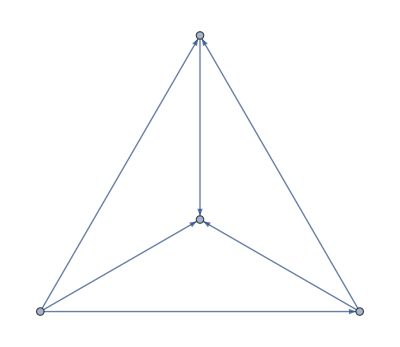
```mathematica
graph =-Graphics-;
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,False,False}

```mathematica
xvars[graph]
tvars[graph]
```

{x[1],x[2],x[3],x[4]}

{t[1->2],t[1->3],t[1->4],t[2->3],t[2->4],t[3->4]}

```mathematica
svars[graph]
dsvars[graph]
```

{-x[1]/(√t[1->2])+x[2]/(√t[1->2]),-x[1]/(√t[1->3])+x[3]/(√t[1->3]),-x[1]/(√t[1->4])+x[4]/(√t[1->4]),-x[2]/(√t[2->3])+x[3]/(√t[2->3]),-x[2]/(√t[2->4])+x[4]/(√t[2->4]),-x[3]/(√t[3->4])+x[4]/(√t[3->4])}

{-dif[x[1]]/(√t[1->2])+dif[x[2]]/(√t[1->2])+(dif[t[1->2]] x[1])/(2 t[1->2]^(3/2))-(dif[t[1->2]] x[2])/(2 t[1->2]^(3/2)),-dif[x[1]]/(√t[1->3])+dif[x[3]]/(√t[1->3])+(dif[t[1->3]] x[1])/(2 t[1->3]^(3/2))-(dif[t[1->3]] x[3])/(2 t[1->3]^(3/2)),-dif[x[1]]/(√t[1->4])+dif[x[4]]/(√t[1->4])+(dif[t[1->4]] x[1])/(2 t[1->4]^(3/2))-(dif[t[1->4]] x[4])/(2 t[1->4]^(3/2)),-dif[x[2]]/(√t[2->3])+dif[x[3]]/(√t[2->3])+(dif[t[2->3]] x[2])/(2 t[2->3]^(3/2))-(dif[t[2->3]] x[3])/(2 t[2->3]^(3/2)),-dif[x[2]]/(√t[2->4])+dif[x[4]]/(√t[2->4])+(dif[t[2->4]] x[2])/(2 t[2->4]^(3/2))-(dif[t[2->4]] x[4])/(2 t[2->4]^(3/2)),-dif[x[3]]/(√t[3->4])+dif[x[4]]/(√t[3->4])+(dif[t[3->4]] x[3])/(2 t[3->4]^(3/2))-(dif[t[3->4]] x[4])/(2 t[3->4]^(3/2))}

```mathematica
somega[graph]
```

0

#### Example: claw

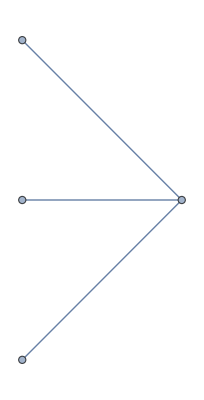
```mathematica
graph =DirectedGraph[-Graphics-,"Acyclic"];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,False,False}

```mathematica
xvars[graph]
tvars[graph]
```

{x[1],x[2],x[3],x[4]}

{t[1->4],t[2->4],t[3->4]}

```mathematica
svars[graph]
dsvars[graph]
```

{-x[1]/(√t[1->4])+x[4]/(√t[1->4]),-x[2]/(√t[2->4])+x[4]/(√t[2->4]),-x[3]/(√t[3->4])+x[4]/(√t[3->4])}

{-dif[x[1]]/(√t[1->4])+dif[x[4]]/(√t[1->4])+(dif[t[1->4]] x[1])/(2 t[1->4]^(3/2))-(dif[t[1->4]] x[4])/(2 t[1->4]^(3/2)),-dif[x[2]]/(√t[2->4])+dif[x[4]]/(√t[2->4])+(dif[t[2->4]] x[2])/(2 t[2->4]^(3/2))-(dif[t[2->4]] x[4])/(2 t[2->4]^(3/2)),-dif[x[3]]/(√t[3->4])+dif[x[4]]/(√t[3->4])+(dif[t[3->4]] x[3])/(2 t[3->4]^(3/2))-(dif[t[3->4]] x[4])/(2 t[3->4]^(3/2))}

```mathematica
smeasure[graph]
stmeasure[graph]
```

-dif[x[1],x[2],x[3]]/(√t[1->4] √t[2->4] √t[3->4])+(dif[t[1->4],x[2],x[3]] x[1])/(2 t[1->4]^(3/2) √t[2->4] √t[3->4])-(dif[t[2->4],x[1],x[3]] x[2])/(2 √t[1->4] t[2->4]^(3/2) √t[3->4])-(dif[t[1->4],t[2->4],x[3]] x[1] x[2])/(4 t[1->4]^(3/2) t[2->4]^(3/2) √t[3->4])+(dif[t[3->4],x[1],x[2]] x[3])/(2 √t[1->4] √t[2->4] t[3->4]^(3/2))+(dif[t[1->4],t[3->4],x[2]] x[1] x[3])/(4 t[1->4]^(3/2) √t[2->4] t[3->4]^(3/2))-(dif[t[2->4],t[3->4],x[1]] x[2] x[3])/(4 √t[1->4] t[2->4]^(3/2) t[3->4]^(3/2))+(dif[t[1->4],t[2->4],t[3->4]] x[1] x[2] x[3])/(8 t[1->4]^(3/2) t[2->4]^(3/2) t[3->4]^(3/2))

-1/(√t[1->4] √t[2->4] √t[3->4])

```mathematica
somega[graph]//printBeauty
```

-(π^(3/2) √t_14 √t_34)/(√(t_14 t_34))

#### Example: 4-path

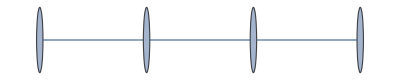
```mathematica
graph =DirectedGraph[-Graphics-,"Acyclic"];
graph//print
lamanQall[UndirectedGraph[graph]]
```

-Graphics-

{False,False,False,False,False,False}

```mathematica
xvars[graph]
tvars[graph]
```

{x[1],x[2],x[3],x[4]}

{t[1->2],t[2->3],t[3->4]}

```mathematica
svars[graph]
dsvars[graph]
```

{-x[1]/(√t[1->2])+x[2]/(√t[1->2]),-x[2]/(√t[2->3])+x[3]/(√t[2->3]),-x[3]/(√t[3->4])+x[4]/(√t[3->4])}

{-dif[x[1]]/(√t[1->2])+dif[x[2]]/(√t[1->2])+(dif[t[1->2]] x[1])/(2 t[1->2]^(3/2))-(dif[t[1->2]] x[2])/(2 t[1->2]^(3/2)),-dif[x[2]]/(√t[2->3])+dif[x[3]]/(√t[2->3])+(dif[t[2->3]] x[2])/(2 t[2->3]^(3/2))-(dif[t[2->3]] x[3])/(2 t[2->3]^(3/2)),-dif[x[3]]/(√t[3->4])+dif[x[4]]/(√t[3->4])+(dif[t[3->4]] x[3])/(2 t[3->4]^(3/2))-(dif[t[3->4]] x[4])/(2 t[3->4]^(3/2))}

```mathematica
smeasure[graph]
stmeasure[graph]
```

-dif[x[1],x[2],x[3]]/(√t[1->2] √t[2->3] √t[3->4])+(dif[t[1->2],x[2],x[3]] x[1])/(2 t[1->2]^(3/2) √t[2->3] √t[3->4])-(dif[t[2->3],x[1],x[3]] x[2])/(2 √t[1->2] t[2->3]^(3/2) √t[3->4])+(dif[t[2->3],x[2],x[3]] x[2])/(2 √t[1->2] t[2->3]^(3/2) √t[3->4])-(dif[t[1->2],x[2],x[3]] x[2])/(2 t[1->2]^(3/2) √t[2->3] √t[3->4])-(dif[t[1->2],t[2->3],x[3]] x[1] x[2])/(4 t[1->2]^(3/2) t[2->3]^(3/2) √t[3->4])+(dif[t[1->2],t[2->3],x[3]] x[2]^2)/(4 t[1->2]^(3/2) t[2->3]^(3/2) √t[3->4])+(dif[t[3->4],x[1],x[2]] x[3])/(2 √t[1->2] √t[2->3] t[3->4]^(3/2))-(dif[t[3->4],x[1],x[3]] x[3])/(2 √t[1->2] √t[2->3] t[3->4]^(3/2))+(dif[t[3->4],x[2],x[3]] x[3])/(2 √t[1->2] √t[2->3] t[3->4]^(3/2))+(dif[t[2->3],x[1],x[3]] x[3])/(2 √t[1->2] t[2->3]^(3/2) √t[3->4])-(dif[t[2->3],x[2],x[3]] x[3])/(2 √t[1->2] t[2->3]^(3/2) √t[3->4])+(dif[t[1->2],t[3->4],x[2]] x[1] x[3])/(4 t[1->2]^(3/2) √t[2->3] t[3->4]^(3/2))-(dif[t[1->2],t[3->4],x[3]] x[1] x[3])/(4 t[1->2]^(3/2) √t[2->3] t[3->4]^(3/2))+(dif[t[1->2],t[2->3],x[3]] x[1] x[3])/(4 t[1->2]^(3/2) t[2->3]^(3/2) √t[3->4])-(dif[t[2->3],t[3->4],x[1]] x[2] x[3])/(4 √t[1->2] t[2->3]^(3/2) t[3->4]^(3/2))+(dif[t[2->3],t[3->4],x[2]] x[2] x[3])/(4 √t[1->2] t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[1->2],t[3->4],x[2]] x[2] x[3])/(4 t[1->2]^(3/2) √t[2->3] t[3->4]^(3/2))+(dif[t[1->2],t[3->4],x[3]] x[2] x[3])/(4 t[1->2]^(3/2) √t[2->3] t[3->4]^(3/2))-(dif[t[1->2],t[2->3],x[3]] x[2] x[3])/(4 t[1->2]^(3/2) t[2->3]^(3/2) √t[3->4])+(dif[t[1->2],t[2->3],t[3->4]] x[1] x[2] x[3])/(8 t[1->2]^(3/2) t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[1->2],t[2->3],t[3->4]] x[2]^2 x[3])/(8 t[1->2]^(3/2) t[2->3]^(3/2) t[3->4]^(3/2))+(dif[t[2->3],t[3->4],x[1]] x[3]^2)/(4 √t[1->2] t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[2->3],t[3->4],x[2]] x[3]^2)/(4 √t[1->2] t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[1->2],t[2->3],t[3->4]] x[1] x[3]^2)/(8 t[1->2]^(3/2) t[2->3]^(3/2) t[3->4]^(3/2))+(dif[t[1->2],t[2->3],t[3->4]] x[2] x[3]^2)/(8 t[1->2]^(3/2) t[2->3]^(3/2) t[3->4]^(3/2))

-1/(√t[1->2] √t[2->3] √t[3->4])

```mathematica
somega[graph]
```

-(π^(3/2) √(t[1->2] t[2->3] t[3->4]))/(√t[1->2] √t[2->3] √t[3->4])

## Defect example

### A: T = 2, H = 0, T ∂ = 1

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point to be at the origin*)
```

-Graphics-

The coordinates of the four operator insertions are 
(x[1,1],x[1,2]), (x[2], 0), (x[3], 0), (0, 0)

```mathematica
α = (smeasure[graph]);
fullMeasure = wedge[α/.{x[1]->x[1,1]},α/.{x[1]->x[1,2],x[2]->0,x[3]->0}]/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify
(*the first α is along the defect and the second α is normal to the defect*)
(*
in the end, we pick out the terms that have dif[t, t, x[1,1],x[1,2],x[2],x[3]]
*)
```

((dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]) x[1,2]^2)/(4 t[1->2]^2 t[1->3]^2 t[1->4]^2)

```mathematica
exp1 =sexp[graph]/.{x[4]->0}/.{x[1]->x[1,1]} //Simplify
exp2 =sexp[graph]/.{x[4]->0}/.{x[1]->x[1,2],x[2]->0,x[3]->0}//Simplify
```

(x[2]-x[1,1])^2/t[1->2]+(x[3]-x[1,1])^2/t[1->3]+x[1,1]^2/t[1->4]

(1/t[1->2]+1/t[1->3]+1/t[1->4]) x[1,2]^2

```mathematica
tmpA = Adefect[exp1+exp2,{x[1,1],x[1,2],x[2],x[3]}]
```

{{2/t[1->2]+2/t[1->3]+2/t[1->4],0,-2/t[1->2],-2/t[1->3]},{0,2 (1/t[1->2]+1/t[1->3]+1/t[1->4]),0,0},{-2/t[1->2],0,2/t[1->2],0},{-2/t[1->3],0,0,2/t[1->3]}}

```mathematica
ωA = 1/π^3 √((2π)^Length[tmpA]/Det[tmpA])wickdefect[exp1+exp2,{x[1,1],x[1,2],x[2],x[3]}][fullMeasure]//FullSimplify[#, t[1->2]>0&& t[1->3]>0&& t[1->4]>0]&
```

(dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4])/(8 π (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))

```mathematica
ωAperp = -(t[1->2] t[1->3] t[1->4])/(8 π (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))dtttt[{t[1->2],t[1->3],t[1->4]}];
ωApara =1//FullSimplify
ωA/(ωAperp*ωApara)//Simplify
```

1

1

```mathematica
-(t[1->2] t[1->3] t[1->4])/(8 π (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))//printBeauty
```

-(t_12 t_13 t_14)/(8 π (t_13 t_14+t_12 (t_13+t_14))^(3/2))

```mathematica
-(t[1->2] dif[t[13],t[14]])/(8 π (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

-dif[T[13],T[14]]/(8 π (T[14]+T[13] (1+T[14]))^(3/2))

```mathematica
Integrate[-1/(8π(x+y+x y)^(3/2)),{x,0,∞},{y,0,∞}]
```

-1/4

### B: T = 2, H = 0, T ∂ = 1, with two defect edges

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point to be at the origin*)
```

-Graphics-

```mathematica
graphDefect = Graph[{2,3,4},{2->3,3->4}];
graphDefect//print
```

-Graphics-

The coordinates of the four operator insertions are 
(x[1,1],x[1,2]), (x[2], 0), (x[3], 0), (0, 0)

```mathematica
α = (smeasure[graph]);
αDefect = (smeasure[graphDefect]);

fullMeasure = wedge[α/.{x[1]->x[1,1]},α/.{x[1]->x[1,2],x[2]->0,x[3]->0}, αDefect]/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify
(*the first α is along the defect
 the second α is normal to the defect
  the αDefect is from the defect propagators*)
(*
in the end, we pick out the terms that have dif[t, t, x[1,1],x[1,2],x[2],x[3]]
*)
```

((dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]-dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]+dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]-dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]+dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]) (x[2]-x[3]) x[3] x[1,2]^2)/(16 t[1->2]^2 t[1->3]^2 t[1->4]^2 t[2->3]^(3/2) t[3->4]^(3/2))

```mathematica
exp1 =sexp[graph]/.{x[4]->0}/.{x[1]->x[1,1]}//Simplify;
exp2 =sexp[graph]/.{x[4]->0}/.{x[1]->x[1,2],x[2]->0,x[3]->0}//Simplify;
expDefect = sexp[graphDefect]//Simplify;
```

```mathematica
tmpA = Adefect[exp1+exp2+expDefect,{x[1,1],x[1,2],x[2],x[3]}]//Simplify
```

{{2 (1/t[1->2]+1/t[1->3]+1/t[1->4]),0,-2/t[1->2],-2/t[1->3]},{0,2 (1/t[1->2]+1/t[1->3]+1/t[1->4]),0,0},{-2/t[1->2],0,2 (1/t[1->2]+1/t[2->3]),-2/t[2->3]},{-2/t[1->3],0,-2/t[2->3],2 (1/t[1->3]+1/t[2->3]+1/t[3->4])}}

```mathematica
ωB = 1/π^4 √((2π)^Length[tmpA]/Det[tmpA])1/2 Nest[
wickdefect[exp1+exp2+expDefect,{x[1,1],x[1,2],x[2],x[3]}][#]&,
fullMeasure,
2]//FullSimplify[#, t[1->2]>0&& t[1->3]>0&& t[1->4]>0&& t[2->3]>0&& t[3->4]>0]&
```

(t[1->3] (-dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]+dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]-dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]+dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]-dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]))/(64 π^2 ((t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4])) (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4])))^(3/2))

```mathematica
ωB/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14],t[23],t[34]]-> t[12]^4 dif[T[13],T[14],T[23],T[34]],dif[t[12],__]->0}/.{t[13]->T[13]t[12],t[14]->T[14]t[12],t[23]->T[23]t[12],t[34]->T[34]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

-(dif[T[13],T[14],T[23],T[34]] T[13])/(64 π^2 ((T[14]+T[13] (1+T[14])) ((1+T[23]) (T[14]+T[34])+T[13] (1+T[14]+T[23]+T[34])))^(3/2))

```mathematica
Integrate[-((*dif[T[13],T[14],T[23],T[34]] *)T[13])/(2 π^2 ((T[14]+T[13] (1+T[14])) ((1+T[23]) (T[14]+T[34])+T[13] (1+T[14]+T[23]+T[34])))^(3/2)),{T[13],0,∞},{T[14],0,∞},{T[23],0,∞},{T[34],0,∞}]
```

-2/3

```mathematica
(ωB/.{t[i_->j_]:>t[10i+j]})/dtttt[{t[12], t[13],t[14],t[23],t[34]}]//printBeauty
```

(t_12 t_13^2 t_14 t_23 t_34)/(64 π^2 ((t_13 t_14+t_12 (t_13+t_14)) (t_23 (t_14+t_34)+t_12 (t_13+t_14+t_34)+t_13 (t_14+t_23+t_34)))^(3/2))

```mathematica
ωBpara = ((dif[t[1->2],t[1->4]]+dif[t[1->2],t[3->4]]-dif[t[1->4],t[2->3]]+dif[t[2->3],t[3->4]]) t[1->3]-(dif[t[1->3],t[1->4]]+dif[t[1->3],t[3->4]]) (t[1->2]+t[2->3])-(dif[t[1->2],t[1->3]]-dif[t[1->3],t[2->3]]) (t[1->4]+t[3->4]))/(-8π (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(3/2));
ωBperp =ωAperp;
```

```mathematica
wedge[ωBpara,ωBperp]/ωB/.{t[i_->j_]:>t[10i+j]}(*/dtttt[{t[12], t[13],t[14],t[23],t[34]}]*)//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0&& t[23]>0&& t[34]>0]&
```

1

```mathematica
ωBpara/.{t[i_->j_]:>t[10i+j]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0&& t[23]>0&& t[34]>0]&
%/.t[a_]:>Subscript[t,a]/.{dif[aa__]:>Wedge[aa]}
```

(-((dif[t[12],t[14]]+dif[t[12],t[34]]-dif[t[14],t[23]]+dif[t[23],t[34]]) t[13])+(dif[t[13],t[14]]+dif[t[13],t[34]]) (t[12]+t[23])+(dif[t[12],t[13]]-dif[t[13],t[23]]) (t[14]+t[34]))/(8 π (t[23] (t[14]+t[34])+t[12] (t[13]+t[14]+t[34])+t[13] (t[14]+t[23]+t[34]))^(3/2))

((t_14+t_34) (t_12⋀t_13-t_13⋀t_23)+(t_12+t_23) (t_13⋀t_14+t_13⋀t_34)-t_13 (t_12⋀t_14+t_12⋀t_34-t_14⋀t_23+t_23⋀t_34))/(8 π (t_23 (t_14+t_34)+t_12 (t_13+t_14+t_34)+t_13 (t_14+t_23+t_34))^(3/2))

### C: T = 1, H = 1, T ∂ = 1

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point (4) to be at the origin*)
(*point(1) is in the bulk*)
```

-Graphics-

(x, z, zb)
the coordinates of four points are
(x[1], z[1], zb[1]) (x[2], 0, 0) (x[3], 0, 0) (0, 0, 0)

```mathematica
α = (smeasure[graph]);
(*topological part of the measure*)
(*/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify*)
```

```mathematica
ρ = ymeasure[graph]/.{zb[2]->0,zb[3]->0}/.changeEdgeLabel[graph]
```

ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) (-(dif[t[1->3],t[1->4],zb[1]] zb[1]^2)/(t[1->2] t[1->3]^2 t[1->4]^2)+(dif[t[1->2],t[1->4],zb[1]] zb[1]^2)/(t[1->2]^2 t[1->3] t[1->4]^2)-(dif[t[1->2],t[1->3],zb[1]] zb[1]^2)/(t[1->2]^2 t[1->3]^2 t[1->4])+(dif[t[1->2],t[1->3],t[1->4]] zb[1]^3)/(t[1->2]^2 t[1->3]^2 t[1->4]^2))

```mathematica
fullMeasure = wedge[α,ρ]/.con[x[1],x[2],x[3],zb[1]]
```

-(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) (-(dif[t[1->3],t[1->4]] zb[1]^2)/(t[1->2] t[1->3]^2 t[1->4]^2)+(dif[t[1->2],t[1->4]] zb[1]^2)/(t[1->2]^2 t[1->3] t[1->4]^2)-(dif[t[1->2],t[1->3]] zb[1]^2)/(t[1->2]^2 t[1->3]^2 t[1->4])))/(√t[1->2] √t[1->3] √t[1->4])

```mathematica
exp1 =sexp[graph]/.{x[4]->0}/.changeEdgeLabel[graph]//Simplify
exp2 =xyexp[graph]/.{zb[2]->0,zb[3]->0,z[2]->0,z[3]->0,zb[4]->0,z[4]->0}/.changeEdgeLabel[graph]//Simplify
```

x[1]^2/t[1->4]+(x[1]-x[2])^2/t[1->2]+(x[1]-x[3])^2/t[1->3]

zb[1] ((z[1]-δ[1->2])/t[1->2]+(z[1]-δ[1->3])/t[1->3]+(z[1]-δ[1->4])/t[1->4])

```mathematica
tmpA = Adefect[exp1+exp2,{x[1],x[2],x[3]},{z[1]},{zb[1]}]
```

{{{2/t[1->2]+2/t[1->3]+2/t[1->4],-2/t[1->2],-2/t[1->3]},{-2/t[1->2],2/t[1->2],0},{-2/t[1->3],0,2/t[1->3]}},{{1/t[1->2]+1/t[1->3]+1/t[1->4]}}}

```mathematica
1/π^(3/2)√((2π)^Length[tmpA[[1]]]/Det[tmpA[[1]]])√((2π)^(2Length[tmpA[[2]]])/(4 Det[tmpA[[2]]]^2))1/2 Nest[
wickdefect[exp1+exp2,{x[1],x[2],x[3]},{z[1]},{zb[1]}][#]&,
fullMeasure,
2
]//FullSimplify[#,t[1->4]>0&&t[1->2]>0&&t[1->3]>0]&
ωC= %/.{z[i_]:>0}
```

(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) π t[1->2] t[1->3] t[1->4] (dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]) λ[1]^2)/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3

(π t[1->2] t[1->3] t[1->4] (dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]) λ[1]^2)/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3

```mathematica
ωC/dtttt[{t[1->2],t[1->3],t[1->4]}]//FullSimplify
%//printBeauty
```

-(π t[1->2]^2 t[1->3]^2 t[1->4]^2 λ[1]^2)/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3

-(π t_12^2 t_13^2 t_14^2 λ[1]^2)/(t_13 t_14+t_12 (t_13+t_14))^3

```mathematica
(dif[t[1->3],t[1->4]] t[1->2]^2 t[1->3] t[1->4] λ[1]^2)/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

(dif[T[13],T[14]] T[13] T[14] λ[1]^2)/(T[14]+T[13] (1+T[14]))^3

```mathematica
Integrate[(x y)/(x+y+x y)^3,{x,0,∞},{y,0,∞}]
```

1/2

### D: T = 1, H = 1, T ∂ = 1, with two defect edges

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point (4) to be at the origin*)
(*point(1) is in the bulk*)
```

-Graphics-

(x, z, zb)
the coordinates of four points are
(x[1], z[1], zb[1]) (x[2], 0, 0) (x[3], 0, 0) (0, 0, 0)

```mathematica
graphDefect = Graph[{2,3,4},{2->3,3->4}];
graphDefect//print
```

-Graphics-

```mathematica
α = (smeasure[graph]);
αDefect = (smeasure[graphDefect]);
(*topological part of the measure*)
(*/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify*)
ρ = ymeasure[graph]/.{zb[2]->0,zb[3]->0}/.changeEdgeLabel[graph];
fullMeasure = wedge[α,ρ,αDefect]/.con[x[1],x[2],x[3],zb[1]]
```

-(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3],t[1->4],t[3->4]] x[2] x[3] zb[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(5/2) t[1->4]^(5/2) √t[2->3] t[3->4]^(3/2))+(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3],t[1->4],t[2->3]] x[2] x[3] zb[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(5/2) t[1->4]^(5/2) t[2->3]^(3/2) √t[3->4])+(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3],t[1->4],t[3->4]] x[3]^2 zb[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(5/2) t[1->4]^(5/2) √t[2->3] t[3->4]^(3/2))-(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3],t[1->4],t[2->3]] x[3]^2 zb[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(5/2) t[1->4]^(5/2) t[2->3]^(3/2) √t[3->4])-1/(√t[1->2] √t[1->3] √t[1->4])ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) (-(dif[t[1->3],t[1->4],t[2->3],t[3->4]] x[2] x[3] zb[1]^2)/(4 t[1->2] t[1->3]^2 t[1->4]^2 t[2->3]^(3/2) t[3->4]^(3/2))+(dif[t[1->2],t[1->4],t[2->3],t[3->4]] x[2] x[3] zb[1]^2)/(4 t[1->2]^2 t[1->3] t[1->4]^2 t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[1->2],t[1->3],t[2->3],t[3->4]] x[2] x[3] zb[1]^2)/(4 t[1->2]^2 t[1->3]^2 t[1->4] t[2->3]^(3/2) t[3->4]^(3/2)))-1/(√t[1->2] √t[1->3] √t[1->4])ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) ((dif[t[1->3],t[1->4],t[2->3],t[3->4]] x[3]^2 zb[1]^2)/(4 t[1->2] t[1->3]^2 t[1->4]^2 t[2->3]^(3/2) t[3->4]^(3/2))-(dif[t[1->2],t[1->4],t[2->3],t[3->4]] x[3]^2 zb[1]^2)/(4 t[1->2]^2 t[1->3] t[1->4]^2 t[2->3]^(3/2) t[3->4]^(3/2))+(dif[t[1->2],t[1->3],t[2->3],t[3->4]] x[3]^2 zb[1]^2)/(4 t[1->2]^2 t[1->3]^2 t[1->4] t[2->3]^(3/2) t[3->4]^(3/2)))

```mathematica
exp1 =sexp[graph]/.{x[4]->0}//Simplify
exp2 =xyexp[graph]/.{zb[2]->0,zb[3]->0,z[2]->0,z[3]->0,zb[4]->0,z[4]->0}//Simplify
expDefect = sexp[graphDefect]//Simplify
```

x[1]^2/t[1->4]+(x[1]-x[2])^2/t[1->2]+(x[1]-x[3])^2/t[1->3]

zb[1] ((z[1]-δ[1->2])/t[1->2]+(z[1]-δ[1->3])/t[1->3]+(z[1]-δ[1->4])/t[1->4])

(t[3->4] (x[2]-x[3])^2+t[2->3] (x[3]-x[4])^2)/(t[2->3] t[3->4])

```mathematica
tmpA = Adefect[exp1+exp2+expDefect,{x[1],x[2],x[3]},{z[1]},{zb[1]}]
```

{{{2/t[1->2]+2/t[1->3]+2/t[1->4],-2/t[1->2],-2/t[1->3]},{-2/t[1->2],2/t[1->2]+2/t[2->3],-2/t[2->3]},{-2/t[1->3],-2/t[2->3],2/t[1->3]+(2 t[2->3]+2 t[3->4])/(t[2->3] t[3->4])}},{{1/t[1->2]+1/t[1->3]+1/t[1->4]}}}

```mathematica
1/π^(5/2)√((2π)^Length[tmpA[[1]]]/Det[tmpA[[1]]])√((2π)^(2Length[tmpA[[2]]])/(4 Det[tmpA[[2]]]^2))1/Factorial[3] Nest[
wickdefect[exp1+exp2+expDefect,{x[1],x[2],x[3]},{z[1]},{zb[1]}][#]&,
fullMeasure,
3
]//FullSimplify[#,t[1->2]>0&& t[1->3]>0&& t[1->4]>0&& t[2->3]>0&& t[3->4]>0]&
ωD = %/.{z[i_]:>0}
```

-((ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) t[1->2] t[1->3]^2 t[1->4] (dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]-dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]+dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]-dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]+dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]) λ[1]^2)/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3 (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(3/2)))

-((t[1->2] t[1->3]^2 t[1->4] (dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]-dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]+dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]-dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]+dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]) λ[1]^2)/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3 (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(3/2)))

```mathematica
(dif[t[1->3],t[1->4]] t[1->2]^2 t[1->3] t[1->4] λ[1]^2)/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

(dif[T[13],T[14]] T[13] T[14] λ[1]^2)/(T[14]+T[13] (1+T[14]))^3

```mathematica
Integrate[(x y)/(x+y+x y)^3,{x,0,∞},{y,0,∞}]
```

1/2

```mathematica
ωDpara = ωBpara;
ωDperp =ωC;
```

```mathematica
ωD==wedge[ωDpara,ωDperp]//Simplify
```

True

```mathematica
ωD/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

(T[13]^2 T[14] (dif[t[12],t[12] T[13],t[12] T[14],t[34]] t[23]-dif[t[12],t[12] T[13],t[12] T[14],t[23]] t[34]-t[12] (dif[t[12] T[13],t[12] T[14],t[23],t[34]]-dif[t[12],t[12] T[14],t[23],t[34]] T[13]+dif[t[12],t[12] T[13],t[23],t[34]] T[14])) λ[1]^2)/(8 t[12]^2 (T[14]+T[13] (1+T[14]))^3 (t[23] t[34]+t[12]^2 (T[14]+T[13] (1+T[14]))+t[12] (t[34] (1+T[13])+t[23] (T[13]+T[14])))^(3/2))

```mathematica
ωD/dtttt[{t[1->2],t[1->3],t[1->4],t[2->3],t[3->4]}]//FullSimplify
%/.{t[i_->j_]:>t[10i+j]}/.{t[a_]:>Subscript[t,a] }//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

(t[1->2]^2 t[1->3]^3 t[1->4]^2 t[2->3] t[3->4] λ[1]^2)/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^3 (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(3/2))

(t_12^2 t_13^3 t_14^2 t_23 t_34 λ[1]^2)/(8 (t_13 t_14+t_12 (t_13+t_14))^3 (t_23 (t_14+t_34)+t_12 (t_13+t_14+t_34)+t_13 (t_14+t_23+t_34))^(3/2))

### E: T = 1, H = 1, H ∂ = 1

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point (4) to be at the origin*)
(*point(1) is in the bulk*)
```

-Graphics-

(x, z, zb)
the coordinates of four points are
(x[1], z[1], zb[1]) (0, z[2], zb[2]) (0, z[3], zb[3]) (0, 0, 0)

```mathematica
α = (smeasure[graph])/.{x[2]->0,x[3]->0,x[4]->0};
(*topological part of the measure*)
(*/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify*)
```

```mathematica
ρ = ymeasure[graph]/.{zb[4]->0};
```

```mathematica
fullMeasure = wedge[α,ρ]/.con[x[1],zb[1],zb[2],zb[3]]
```

(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->3],t[1->4]] x[1]^2)/(4 t[1->2]^(3/2) t[1->3]^(5/2) t[1->4]^(5/2))-(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->4]] x[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(3/2) t[1->4]^(5/2))+(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3]] x[1]^2)/(4 t[1->2]^(5/2) t[1->3]^(5/2) t[1->4]^(3/2))

```mathematica
exp1 =sexp[graph]/.{x[2]->0,x[3]->0,x[4]->0}//Simplify
exp2 =xyexp[graph]/.{zb[4]->0,z[4]->0}//Simplify
```

(1/t[1->2]+1/t[1->3]+1/t[1->4]) x[1]^2

((zb[1]-zb[2]) (z[1]-z[2]-δ[1->2]))/t[1->2]+((zb[1]-zb[3]) (z[1]-z[3]-δ[1->3]))/t[1->3]+(zb[1] (z[1]-δ[1->4]))/t[1->4]

```mathematica
tmpA = Adefect[exp1+exp2,{x[1]},{z[1],z[2],z[3]},{zb[1],zb[2],zb[3]}]
```

{{{2 (1/t[1->2]+1/t[1->3]+1/t[1->4])}},{{1/t[1->2]+1/t[1->3]+1/t[1->4],-1/t[1->2],-1/t[1->3]},{-1/t[1->2],1/t[1->2],0},{-1/t[1->3],0,1/t[1->3]}}}

```mathematica
1/π^(3/2)√((2π)^Length[tmpA[[1]]]/Det[tmpA[[1]]])√((2π)^(2Length[tmpA[[2]]])/(4^3 Det[tmpA[[2]]]^2))Nest[
wickdefect[exp1+exp2,{x[1]},{z[1],z[2],z[3]},{zb[1],zb[2],zb[3]}][#]&,
fullMeasure,
1
]//FullSimplify[#,t[1->4]>0&&t[1->2]>0&&t[1->3]>0]&
ωE =%/.{z[i_]:>0}
```

(ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) π^2 (dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]))/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))

(π^2 (dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]))/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))

```mathematica
(dif[t[1->3],t[1->4]] t[1->2])/(t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2)/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&
```

dif[T[13],T[14]]/(T[14]+T[13] (1+T[14]))^(3/2)

```mathematica
Integrate[1/(x+y+x y)^(3/2),{x,0,∞},{y,0,∞}]
```

2 π

```mathematica
ωEperp = ωAperp;
ωEpara = 1;
```

```mathematica
ωE/(ωEperp*ωEpara)//FullSimplify
```

(π^2 (dif[t[1->3],t[1->4]] t[1->2]-dif[t[1->2],t[1->4]] t[1->3]+dif[t[1->2],t[1->3]] t[1->4]))/(8 ωAperp (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))

### F: T = 1, H = 1, H ∂ = 1, with two defect edges

```mathematica
graph = Graph[{1,2,3,4},{1->2,1->3,1->4}];
graph//print
(*note that the convention is to choose last point (4) to be at the origin*)
(*point(1) is in the bulk*)
```

-Graphics-

(x, z, zb)
the coordinates of four points are
(x[1], z[1], zb[1]) (0, z[2], zb[2]) (0, z[3], zb[3]) (0, 0, 0)

```mathematica
graphDefect = Graph[{2,3,4},{2->3,3->4}];
graphDefect//print
```

-Graphics-

```mathematica
α = (smeasure[graph])/.{x[2]->0,x[3]->0,x[4]->0};
ρDefect = (ymeasure[graphDefect])/.{zb[4]->0};
ρ = ymeasure[graph]/.{zb[4]->0};
fullMeasure = wedge[α,ρ,ρDefect]/.con[x[1],zb[1],zb[2],zb[3]];
holMeasure =  wedge[ρ,ρDefect]/.con[zb[1],zb[2],zb[3]]
(*topological part of the measure*)
(*/.con[x[1,1],x[1,2],x[2],x[3]]//FullSimplify*)
```

ⅇ^(z[1] λ[1]+z[2] λ[2]+z[3] λ[3]) (-(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->3],t[1->4]] zb[1]^2)/(t[1->2] t[1->3]^2 t[1->4]^2 t[2->3] t[3->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->4]] zb[1]^2)/(t[1->2]^2 t[1->3] t[1->4]^2 t[2->3] t[3->4])-(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3]] zb[1]^2)/(t[1->2]^2 t[1->3]^2 t[1->4] t[2->3] t[3->4])-(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->4]] zb[1] zb[2])/(t[1->2]^2 t[1->3] t[1->4]^2 t[2->3] t[3->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3]] zb[1] zb[2])/(t[1->2]^2 t[1->3]^2 t[1->4] t[2->3] t[3->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->4],t[3->4]] zb[1] zb[3])/(t[1->2] t[1->3] t[1->4]^2 t[2->3] t[3->4]^2)-(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[3->4]] zb[1] zb[3])/(t[1->2]^2 t[1->3] t[1->4] t[2->3] t[3->4]^2)+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->3],t[1->4]] zb[1] zb[3])/(t[1->2] t[1->3]^2 t[1->4]^2 t[2->3] t[3->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3]] zb[1] zb[3])/(t[1->2]^2 t[1->3]^2 t[1->4] t[2->3] t[3->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[3->4]] zb[2] zb[3])/(t[1->2]^2 t[1->3] t[1->4] t[2->3] t[3->4]^2)-(ⅇ^(z[2] λ[2]+z[3] λ[3]) dif[t[1->2],t[1->3]] zb[2] zb[3])/(t[1->2]^2 t[1->3]^2 t[1->4] t[2->3] t[3->4])-(ⅇ^(z[2] λ[2]+z[3] λ[3]) zb[1] (-(dif[t[1->3],t[2->3]] zb[2])/(t[2->3]^2 t[3->4])-(dif[t[1->3],t[3->4]] zb[3])/(t[2->3] t[3->4]^2)+(dif[t[1->3],t[2->3]] zb[3])/(t[2->3]^2 t[3->4])))/(t[1->2] t[1->3]^2 t[1->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) zb[3] (-(dif[t[1->3],t[2->3]] zb[2])/(t[2->3]^2 t[3->4])-(dif[t[1->3],t[3->4]] zb[3])/(t[2->3] t[3->4]^2)+(dif[t[1->3],t[2->3]] zb[3])/(t[2->3]^2 t[3->4])))/(t[1->2] t[1->3]^2 t[1->4])+(ⅇ^(z[2] λ[2]+z[3] λ[3]) zb[1] (-(dif[t[1->4],t[2->3]] zb[2])/(t[2->3]^2 t[3->4])-(dif[t[1->4],t[3->4]] zb[3])/(t[2->3] t[3->4]^2)+(dif[t[1->4],t[2->3]] zb[3])/(t[2->3]^2 t[3->4])))/(t[1->2] t[1->3] t[1->4]^2)-(ⅇ^(z[2] λ[2]+z[3] λ[3]) ((dif[t[2->3],t[3->4]] zb[2] zb[3])/(t[2->3]^2 t[3->4]^2)-(dif[t[2->3],t[3->4]] zb[3]^2)/(t[2->3]^2 t[3->4]^2)))/(t[1->2] t[1->3] t[1->4]))

```mathematica
exp1 =sexp[graph]/.{x[2]->0,x[3]->0,x[4]->0}//Simplify
exp2 =xyexp[graph]/.{zb[4]->0,z[4]->0}//Simplify
expDefect = xyexp[graphDefect]/.{zb[4]->0,z[4]->0}//Simplify
```

(1/t[1->2]+1/t[1->3]+1/t[1->4]) x[1]^2

((zb[1]-zb[2]) (z[1]-z[2]-δ[1->2]))/t[1->2]+((zb[1]-zb[3]) (z[1]-z[3]-δ[1->3]))/t[1->3]+(zb[1] (z[1]-δ[1->4]))/t[1->4]

((zb[2]-zb[3]) (z[2]-z[3]-δ[2->3]))/t[2->3]+(zb[3] (z[3]-δ[3->4]))/t[3->4]

```mathematica
tmpA = Adefect[exp1+exp2+expDefect,{x[1]},{z[1],z[2],z[3]},{zb[1],zb[2],zb[3]}]
```

{{{2 (1/t[1->2]+1/t[1->3]+1/t[1->4])}},{{1/t[1->2]+1/t[1->3]+1/t[1->4],-1/t[1->2],-1/t[1->3]},{-1/t[1->2],1/t[1->2]+1/t[2->3],-1/t[2->3]},{-1/t[1->3],-1/t[2->3],1/t[1->3]+1/t[2->3]+1/t[3->4]}}}

```mathematica
1/π^(3/2)√((2π)^Length[tmpA[[1]]]/Det[tmpA[[1]]])√((2π)^(2Length[tmpA[[2]]])/(4^3 Det[tmpA[[2]]]))1/Factorial[3] Nest[
wickdefect[exp1+exp2+expDefect,{x[1]},{z[1],z[2],z[3]},{zb[1],zb[2],zb[3]}][#]&,
fullMeasure,
3
]//Simplify[#,t[1->4]>0&&t[1->2]>0&&t[1->3]>0&&t[2->3]>0&&t[3->4]>0]&
ωF =%/.{z[i_]:>0}
```

(ⅇ^(z[1] λ[1]+2 z[2] λ[2]+2 z[3] λ[3]) π^2 (dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]-dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]+dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]-dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]+dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]) (2 t[1->2] (t[1->4]+t[3->4]) λ[2]+t[1->3] (2 t[1->2] λ[2]+t[1->4] (λ[1]+2 λ[2])-2 t[3->4] λ[3])) (t[1->4] t[2->3] (λ[1]+2 (λ[2]+λ[3]))+t[1->3] (2 t[2->3] λ[3]+t[1->4] (λ[1]+2 (λ[2]+λ[3])))+t[1->2] (2 t[1->3] (λ[2]+λ[3])+t[1->4] (λ[1]+2 (λ[2]+λ[3])))))/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2) √(t[1->2] t[1->3] t[1->4] t[2->3] t[3->4]) (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(5/2))

(π^2 (dif[t[1->3],t[1->4],t[2->3],t[3->4]] t[1->2]-dif[t[1->2],t[1->4],t[2->3],t[3->4]] t[1->3]+dif[t[1->2],t[1->3],t[2->3],t[3->4]] t[1->4]-dif[t[1->2],t[1->3],t[1->4],t[3->4]] t[2->3]+dif[t[1->2],t[1->3],t[1->4],t[2->3]] t[3->4]) (2 t[1->2] (t[1->4]+t[3->4]) λ[2]+t[1->3] (2 t[1->2] λ[2]+t[1->4] (λ[1]+2 λ[2])-2 t[3->4] λ[3])) (t[1->4] t[2->3] (λ[1]+2 (λ[2]+λ[3]))+t[1->3] (2 t[2->3] λ[3]+t[1->4] (λ[1]+2 (λ[2]+λ[3])))+t[1->2] (2 t[1->3] (λ[2]+λ[3])+t[1->4] (λ[1]+2 (λ[2]+λ[3])))))/(8 (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2) √(t[1->2] t[1->3] t[1->4] t[2->3] t[3->4]) (t[2->3] (t[1->4]+t[3->4])+t[1->2] (t[1->3]+t[1->4]+t[3->4])+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(5/2))

```mathematica
√((2π)^(2Length[tmpA[[2]]])/(4^3 Det[tmpA[[2]]]))1/Factorial[2] Nest[
wickCustomAHol[tmpA[[2]],{z[1],z[2],z[3]},{zb[1],zb[2],zb[3]}][#]&,
holMeasure,
2
]//Simplify[#,t[1->4]>0&&t[1->2]>0&&t[1->3]>0&&t[2->3]>0&&t[3->4]>0]&
ωFpara =%/.{z[i_]:>0};
```

-((ⅇ^(z[1] λ[1]+2 z[2] λ[2]+2 z[3] λ[3]) π^3 (dif[t[1->4],t[2->3]] t[1->2] t[1->3]^2 t[1->4] λ[1]^2-1+427+1-dif[t[1->2],t[1->4]] (1) (-2 t[2->3] (t[1->4]+t[3->4]) λ[2]+t[1->3] (1))))/(√(t[1->2] t[1->3] t[1->4] t[2->3] t[3->4]) (t[2->3] (t[1->4]+t[3->4])+t[1->2] (1)+t[1->3] (t[1->4]+t[2->3]+t[3->4]))^(5/2)))
 |  |  |  |

```mathematica
ωFpara//printBeauty
```

-((π^3 (dif[t_14,t_23] t_12 t_13^2 t_14 λ[1]^2-dif[t_13,t_34] t_12^2 t_14^2 λ[1]^2+dif[t_12,t_13] t_12 t_13 t_14^2 λ[1]^2+dif[t_12,t_34] t_12 t_13 t_14^2 λ[1]^2-dif[t_13,t_23] t_12 t_13 t_14^2 λ[1]^2-dif[t_13,t_34] t_12 t_13 t_14^2 λ[1]^2+dif[t_23,t_34] t_12 t_13 t_14^2 λ[1]^2+dif[t_12,t_34] t_13^2 t_14^2 λ[1]^2+dif[t_23,t_34] t_13^2 t_14^2 λ[1]^2+dif[t_14,t_23] t_13^2 t_14 t_23 λ[1]^2-2 dif[t_13,t_34] t_12 t_14^2 t_23 λ[1]^2+dif[t_12,t_13] t_13 t_14^2 t_23 λ[1]^2+dif[t_12,t_34] t_13 t_14^2 t_23 λ[1]^2-dif[t_13,t_23] t_13 t_14^2 t_23 λ[1]^2-dif[t_13,t_34] t_13 t_14^2 t_23 λ[1]^2+dif[t_23,t_34] t_13 t_14^2 t_23 λ[1]^2-dif[t_13,t_34] t_14^2 t_23^2 λ[1]^2+dif[t_14,t_23] t_12 t_13 t_14 t_34 λ[1]^2+dif[t_14,t_23] t_13^2 t_14 t_34 λ[1]^2+dif[t_14,t_23] t_13 t_14 t_23 t_34 λ[1]^2+2 dif[t_14,t_23] t_12^2 t_13^2 λ[1] λ[2]-2 dif[t_13,t_23] t_12^2 t_13 t_14 λ[1] λ[2]-2 dif[t_13,t_34] t_12^2 t_13 t_14 λ[1] λ[2]+2 dif[t_14,t_23] t_12^2 t_13 t_14 λ[1] λ[2]+2 dif[t_23,t_34] t_12^2 t_13 t_14 λ[1] λ[2]+2 dif[t_12,t_34] t_12 t_13^2 t_14 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_13^2 t_14 λ[1] λ[2]+4 dif[t_23,t_34] t_12 t_13^2 t_14 λ[1] λ[2]-2 dif[t_13,t_23] t_12^2 t_14^2 λ[1] λ[2]-2 dif[t_13,t_34] t_12^2 t_14^2 λ[1] λ[2]+2 dif[t_23,t_34] t_12^2 t_14^2 λ[1] λ[2]+2 dif[t_12,t_34] t_12 t_13 t_14^2 λ[1] λ[2]-2 dif[t_13,t_23] t_12 t_13 t_14^2 λ[1] λ[2]-2 dif[t_13,t_34] t_12 t_13 t_14^2 λ[1] λ[2]+6 dif[t_23,t_34] t_12 t_13 t_14^2 λ[1] λ[2]+2 dif[t_12,t_34] t_13^2 t_14^2 λ[1] λ[2]+4 dif[t_23,t_34] t_13^2 t_14^2 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_13^2 t_23 λ[1] λ[2]-2 dif[t_12,t_13] t_12 t_13 t_14 t_23 λ[1] λ[2]-2 dif[t_12,t_34] t_12 t_13 t_14 t_23 λ[1] λ[2]-2 dif[t_13,t_23] t_12 t_13 t_14 t_23 λ[1] λ[2]-2 dif[t_13,t_34] t_12 t_13 t_14 t_23 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_13 t_14 t_23 λ[1] λ[2]+2 dif[t_23,t_34] t_12 t_13 t_14 t_23 λ[1] λ[2]-2 dif[t_12,t_34] t_13^2 t_14 t_23 λ[1] λ[2]+4 dif[t_14,t_23] t_13^2 t_14 t_23 λ[1] λ[2]-2 dif[t_12,t_13] t_12 t_14^2 t_23 λ[1] λ[2]-2 dif[t_12,t_34] t_12 t_14^2 t_23 λ[1] λ[2]-2 dif[t_13,t_23] t_12 t_14^2 t_23 λ[1] λ[2]-6 dif[t_13,t_34] t_12 t_14^2 t_23 λ[1] λ[2]+2 dif[t_23,t_34] t_12 t_14^2 t_23 λ[1] λ[2]+2 dif[t_12,t_13] t_13 t_14^2 t_23 λ[1] λ[2]-4 dif[t_13,t_23] t_13 t_14^2 t_23 λ[1] λ[2]-4 dif[t_13,t_34] t_13 t_14^2 t_23 λ[1] λ[2]+4 dif[t_23,t_34] t_13 t_14^2 t_23 λ[1] λ[2]-2 dif[t_12,t_13] t_13 t_14 t_23^2 λ[1] λ[2]-2 dif[t_12,t_34] t_13 t_14 t_23^2 λ[1] λ[2]-2 dif[t_12,t_13] t_14^2 t_23^2 λ[1] λ[2]-2 dif[t_12,t_34] t_14^2 t_23^2 λ[1] λ[2]-4 dif[t_13,t_34] t_14^2 t_23^2 λ[1] λ[2]+4 dif[t_14,t_23] t_12^2 t_13 t_34 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_13^2 t_34 λ[1] λ[2]-2 dif[t_13,t_23] t_12^2 t_14 t_34 λ[1] λ[2]+2 dif[t_13,t_34] t_12^2 t_14 t_34 λ[1] λ[2]+2 dif[t_14,t_23] t_12^2 t_14 t_34 λ[1] λ[2]+2 dif[t_23,t_34] t_12^2 t_14 t_34 λ[1] λ[2]-4 dif[t_12,t_13] t_12 t_13 t_14 t_34 λ[1] λ[2]-2 dif[t_12,t_34] t_12 t_13 t_14 t_34 λ[1] λ[2]+2 dif[t_13,t_23] t_12 t_13 t_14 t_34 λ[1] λ[2]+2 dif[t_13,t_34] t_12 t_13 t_14 t_34 λ[1] λ[2]+6 dif[t_14,t_23] t_12 t_13 t_14 t_34 λ[1] λ[2]+2 dif[t_23,t_34] t_12 t_13 t_14 t_34 λ[1] λ[2]-2 dif[t_12,t_34] t_13^2 t_14 t_34 λ[1] λ[2]+4 dif[t_14,t_23] t_13^2 t_14 t_34 λ[1] λ[2]+4 dif[t_14,t_23] t_12 t_13 t_23 t_34 λ[1] λ[2]-2 dif[t_12,t_13] t_12 t_14 t_23 t_34 λ[1] λ[2]-2 dif[t_12,t_34] t_12 t_14 t_23 t_34 λ[1] λ[2]-2 dif[t_13,t_23] t_12 t_14 t_23 t_34 λ[1] λ[2]+2 dif[t_13,t_34] t_12 t_14 t_23 t_34 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_14 t_23 t_34 λ[1] λ[2]+2 dif[t_23,t_34] t_12 t_14 t_23 t_34 λ[1] λ[2]-2 dif[t_12,t_13] t_13 t_14 t_23 t_34 λ[1] λ[2]-4 dif[t_12,t_34] t_13 t_14 t_23 t_34 λ[1] λ[2]+4 dif[t_14,t_23] t_13 t_14 t_23 t_34 λ[1] λ[2]-2 dif[t_12,t_13] t_14 t_23^2 t_34 λ[1] λ[2]-2 dif[t_12,t_34] t_14 t_23^2 t_34 λ[1] λ[2]+2 dif[t_14,t_23] t_12^2 t_34^2 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_13 t_34^2 λ[1] λ[2]+2 dif[t_14,t_23] t_12 t_23 t_34^2 λ[1] λ[2]+4 dif[t_23,t_34] t_12^2 t_13^2 λ[2]^2+8 dif[t_23,t_34] t_12^2 t_13 t_14 λ[2]^2+8 dif[t_23,t_34] t_12 t_13^2 t_14 λ[2]^2+4 dif[t_23,t_34] t_12^2 t_14^2 λ[2]^2+8 dif[t_23,t_34] t_12 t_13 t_14^2 λ[2]^2+4 dif[t_23,t_34] t_13^2 t_14^2 λ[2]^2-4 dif[t_12,t_34] t_12 t_13^2 t_23 λ[2]^2+4 dif[t_14,t_23] t_12 t_13^2 t_23 λ[2]^2-8 dif[t_12,t_34] t_12 t_13 t_14 t_23 λ[2]^2-4 dif[t_13,t_23] t_12 t_13 t_14 t_23 λ[2]^2-4 dif[t_13,t_34] t_12 t_13 t_14 t_23 λ[2]^2+4 dif[t_14,t_23] t_12 t_13 t_14 t_23 λ[2]^2+4 dif[t_23,t_34] t_12 t_13 t_14 t_23 λ[2]^2-4 dif[t_12,t_34] t_13^2 t_14 t_23 λ[2]^2+4 dif[t_14,t_23] t_13^2 t_14 t_23 λ[2]^2-4 dif[t_12,t_34] t_12 t_14^2 t_23 λ[2]^2-4 dif[t_13,t_23] t_12 t_14^2 t_23 λ[2]^2-4 dif[t_13,t_34] t_12 t_14^2 t_23 λ[2]^2+4 dif[t_23,t_34] t_12 t_14^2 t_23 λ[2]^2-4 dif[t_12,t_34] t_13 t_14^2 t_23 λ[2]^2-4 dif[t_13,t_23] t_13 t_14^2 t_23 λ[2]^2-4 dif[t_13,t_34] t_13 t_14^2 t_23 λ[2]^2+4 dif[t_23,t_34] t_13 t_14^2 t_23 λ[2]^2-4 dif[t_12,t_13] t_13 t_14 t_23^2 λ[2]^2-4 dif[t_12,t_34] t_13 t_14 t_23^2 λ[2]^2-4 dif[t_12,t_13] t_14^2 t_23^2 λ[2]^2-4 dif[t_12,t_34] t_14^2 t_23^2 λ[2]^2-4 dif[t_13,t_34] t_14^2 t_23^2 λ[2]^2+4 dif[t_13,t_23] t_12^2 t_13 t_34 λ[2]^2+4 dif[t_13,t_34] t_12^2 t_13 t_34 λ[2]^2+4 dif[t_14,t_23] t_12^2 t_13 t_34 λ[2]^2+4 dif[t_23,t_34] t_12^2 t_13 t_34 λ[2]^2-4 dif[t_12,t_34] t_12 t_13^2 t_34 λ[2]^2+4 dif[t_14,t_23] t_12 t_13^2 t_34 λ[2]^2+4 dif[t_13,t_23] t_12^2 t_14 t_34 λ[2]^2+4 dif[t_13,t_34] t_12^2 t_14 t_34 λ[2]^2+4 dif[t_14,t_23] t_12^2 t_14 t_34 λ[2]^2+4 dif[t_23,t_34] t_12^2 t_14 t_34 λ[2]^2-4 dif[t_12,t_34] t_12 t_13 t_14 t_34 λ[2]^2+4 dif[t_13,t_23] t_12 t_13 t_14 t_34 λ[2]^2+4 dif[t_13,t_34] t_12 t_13 t_14 t_34 λ[2]^2+8 dif[t_14,t_23] t_12 t_13 t_14 t_34 λ[2]^2+4 dif[t_23,t_34] t_12 t_13 t_14 t_34 λ[2]^2-4 dif[t_12,t_34] t_13^2 t_14 t_34 λ[2]^2+4 dif[t_14,t_23] t_13^2 t_14 t_34 λ[2]^2+4 dif[t_12,t_13] t_12 t_13 t_23 t_34 λ[2]^2-4 dif[t_12,t_34] t_12 t_13 t_23 t_34 λ[2]^2+8 dif[t_14,t_23] t_12 t_13 t_23 t_34 λ[2]^2+4 dif[t_12,t_13] t_12 t_14 t_23 t_34 λ[2]^2-4 dif[t_12,t_34] t_12 t_14 t_23 t_34 λ[2]^2-4 dif[t_13,t_23] t_12 t_14 t_23 t_34 λ[2]^2+4 dif[t_13,t_34] t_12 t_14 t_23 t_34 λ[2]^2+4 dif[t_14,t_23] t_12 t_14 t_23 t_34 λ[2]^2+4 dif[t_23,t_34] t_12 t_14 t_23 t_34 λ[2]^2-4 dif[t_12,t_13] t_13 t_14 t_23 t_34 λ[2]^2-8 dif[t_12,t_34] t_13 t_14 t_23 t_34 λ[2]^2+4 dif[t_14,t_23] t_13 t_14 t_23 t_34 λ[2]^2-4 dif[t_12,t_13] t_14 t_23^2 t_34 λ[2]^2-4 dif[t_12,t_34] t_14 t_23^2 t_34 λ[2]^2+4 dif[t_13,t_23] t_12^2 t_34^2 λ[2]^2+4 dif[t_14,t_23] t_12^2 t_34^2 λ[2]^2+4 dif[t_12,t_13] t_12 t_13 t_34^2 λ[2]^2+4 dif[t_14,t_23] t_12 t_13 t_34^2 λ[2]^2+4 dif[t_12,t_13] t_12 t_23 t_34^2 λ[2]^2+4 dif[t_14,t_23] t_12 t_23 t_34^2 λ[2]^2+2 (dif[t_23,t_34] t_12 t_13^2 t_14 λ[1]+dif[t_23,t_34] t_12 t_13 t_14^2 λ[1]+dif[t_23,t_34] t_13^2 t_14^2 λ[1]+dif[t_23,t_34] t_13^2 t_14 t_23 λ[1]+dif[t_23,t_34] t_13 t_14^2 t_23 λ[1]-dif[t_14,t_23] t_12 t_13^2 t_34 λ[1]-2 dif[t_12,t_13] t_12 t_13 t_14 t_34 λ[1]+2 dif[t_13,t_23] t_12 t_13 t_14 t_34 λ[1]+dif[t_14,t_23] t_12 t_13 t_14 t_34 λ[1]-dif[t_23,t_34] t_12 t_13 t_14 t_34 λ[1]+dif[t_14,t_23] t_13^2 t_14 t_34 λ[1]-dif[t_23,t_34] t_13^2 t_14 t_34 λ[1]-dif[t_14,t_23] t_13^2 t_23 t_34 λ[1]-2 dif[t_12,t_13] t_13 t_14 t_23 t_34 λ[1]+2 dif[t_13,t_23] t_13 t_14 t_23 t_34 λ[1]+dif[t_14,t_23] t_13 t_14 t_23 t_34 λ[1]-dif[t_23,t_34] t_13 t_14 t_23 t_34 λ[1]-dif[t_14,t_23] t_12 t_13 t_34^2 λ[1]-dif[t_14,t_23] t_13^2 t_34^2 λ[1]-dif[t_14,t_23] t_13 t_23 t_34^2 λ[1]+2 (dif[t_23,t_34] (t_13 t_14+t_12 (t_13+t_14)) (t_12 (t_13+t_14)+t_14 t_23+t_13 (t_14+t_23))+(dif[t_23,t_34] (t_12-t_13) (t_13 t_14+t_12 (t_13+t_14))+(dif[t_12,t_13]+dif[t_23,t_34]) (-t_13 t_14+t_12 (t_13+t_14)) t_23+dif[t_12,t_13] (t_13+t_14) t_23^2+dif[t_14,t_23] ((t_12+t_13) (t_13 t_14+t_12 (t_13+t_14))+(t_13 (-t_13+t_14)+t_12 (t_13+t_14)) t_23)+dif[t_13,t_23] (t_12^2 (t_13+t_14)+2 t_13 t_14 t_23+t_12 (t_13 t_14+(t_13+t_14) t_23))) t_34+(dif[t_13,t_23] t_12 (t_12-t_13+t_23)+dif[t_14,t_23] (t_12-t_13) (t_12+t_13+t_23)+dif[t_12,t_13] (2 t_12 t_13+(t_12+t_13) t_23+t_23^2)) t_34^2) λ[2]+dif[t_12,t_34] (t_13 t_14 (t_23 (t_14-t_34)+t_12 (t_13+t_14-t_34)+t_13 (t_14+t_23-t_34)) λ[1]-2 ((t_13+t_14) t_23 (t_12 (t_13+t_14)+t_14 t_23+t_13 (t_14+t_23))+(t_12 (t_13+t_14) (2 t_13+t_23)+(t_13+t_23) (2 t_13 t_14+(t_13+t_14) t_23)) t_34) λ[2])+dif[t_13,t_34] (-t_14 (t_12+t_23) (t_23 (t_14-t_34)+t_12 (t_13+t_14-t_34)+t_13 (t_14+t_23-t_34)) λ[1]+2 (-t_14 t_23 (t_12 (t_13+t_14)+t_14 t_23+t_13 (t_14+t_23))+(2 t_12^2 (t_13+t_14)+t_14 t_23 (t_13+t_23)+t_12 (3 t_14 t_23+2 t_13 (t_14+t_23))) t_34) λ[2])) λ[3]-4 t_34 (-((-((dif[t_12,t_34]+dif[t_23,t_34]) t_13)+dif[t_13,t_34] (t_12+t_23)) (t_12 (t_13+t_14)+t_14 t_23+t_13 (t_14+t_23)))+t_13 (-dif[t_12,t_13] (t_12+t_23)+dif[t_13,t_23] (t_12+t_23)+dif[t_14,t_23] (t_12+t_13+t_23)) t_34) λ[3]^2+dif[t_13,t_14] (t_23 (t_14 (λ[1]+2 λ[2])-2 t_34 λ[3])+t_12 (t_14 λ[1]-2 t_34 (λ[2]+λ[3]))) ((t_23 t_34+t_13 (t_23+t_34)) (λ[1]+2 λ[2])+2 (t_13+t_23) t_34 λ[3]+t_12 (t_13 λ[1]+t_34 (λ[1]+2 (λ[2]+λ[3]))))-dif[t_12,t_14] (-2 t_23 (t_14+t_34) λ[2]+t_13 (t_14 λ[1]-2 t_23 λ[2]-2 t_34 (λ[2]+λ[3]))) ((t_23 t_34+t_13 (t_23+t_34)) (λ[1]+2 λ[2])+2 (t_13+t_23) t_34 λ[3]+t_12 (t_13 λ[1]+t_34 (λ[1]+2 (λ[2]+λ[3]))))))/(√(t_12 t_13 t_14 t_23 t_34) (t_23 (t_14+t_34)+t_12 (t_13+t_14+t_34)+t_13 (t_14+t_23+t_34))^(5/2)))

```mathematica
(*/.{t[i_->j_]:>t[10i+j]}/.{dif[t[13],t[14]]-> t[12]^2 dif[T[13],T[14]]}/.{t[13]->T[13]t[12],t[14]->T[14]t[12]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0]&*)
```

```mathematica
ωFperp = ωEperp
```

-(t[1->2] t[1->3] (-dif[t[1->2],t[1->3]]/(t[1->2] t[1->3])+dif[t[1->2],t[1->4]]/(t[1->2] t[1->4])-dif[t[1->3],t[1->4]]/(t[1->3] t[1->4])) t[1->4])/(8 π (t[1->3] t[1->4]+t[1->2] (t[1->3]+t[1->4]))^(3/2))

```mathematica
ωF/(wedge[ωFperp,ωFpara])//FullSimplify
```

-1

```mathematica
ωF/dtttt[{t[1->2],t[1->3],t[1->4],t[2->3],t[3->4]}]/.{t[i_->j_]:>t[10i+j]}//FullSimplify[#, t[12]>0&& t[13]>0&& t[14]>0&& t[23]>0&& t[34]>0]&
ωFcoef = %/.{t[a_]:>Subscript[t,a],λ[a_]:>Subscript[λ,a]}
```

-((π^2 √(t[12] t[13] t[14] t[23] t[34]) (2 t[12] (t[14]+t[34]) λ[2]+t[13] (2 t[12] λ[2]+t[14] (λ[1]+2 λ[2])-2 t[34] λ[3])) (t[14] (t[13]+t[23]) (λ[1]+2 λ[2])+2 (t[14] t[23]+t[13] (t[14]+t[23])) λ[3]+t[12] (2 t[13] (λ[2]+λ[3])+t[14] (λ[1]+2 (λ[2]+λ[3])))))/(8 (t[13] t[14]+t[12] (t[13]+t[14]))^(3/2) (t[23] (t[14]+t[34])+t[12] (t[13]+t[14]+t[34])+t[13] (t[14]+t[23]+t[34]))^(5/2)))

-((π^2 √(t_12 t_13 t_14 t_23 t_34) (2 t_12 (t_14+t_34) λ_2+t_13 (2 t_12 λ_2+t_14 (λ_1+2 λ_2)-2 t_34 λ_3)) (t_14 (t_13+t_23) (λ_1+2 λ_2)+2 (t_14 t_23+t_13 (t_14+t_23)) λ_3+t_12 (2 t_13 (λ_2+λ_3)+t_14 (λ_1+2 (λ_2+λ_3)))))/(8 (t_13 t_14+t_12 (t_13+t_14))^(3/2) (t_23 (t_14+t_34)+t_12 (t_13+t_14+t_34)+t_13 (t_14+t_23+t_34))^(5/2)))

```mathematica
num =- π^2/8 √(Subscript[t, 12] Subscript[t, 13] Subscript[t, 14] Subscript[t, 23] Subscript[t, 34]) (2 Subscript[t, 12] (Subscript[t, 14]+Subscript[t, 34]) Subscript[λ, 2]+Subscript[t, 13] (2 Subscript[t, 12] Subscript[λ, 2]+Subscript[t, 14] (Subscript[λ, 1]+2 Subscript[λ, 2])-2 Subscript[t, 34] Subscript[λ, 3])) (Subscript[t, 14] (Subscript[t, 13]+Subscript[t, 23]) (Subscript[λ, 1]+2 Subscript[λ, 2])+2 (Subscript[t, 14] Subscript[t, 23]+Subscript[t, 13] (Subscript[t, 14]+Subscript[t, 23])) Subscript[λ, 3]+Subscript[t, 12] (2 Subscript[t, 13] (Subscript[λ, 2]+Subscript[λ, 3])+Subscript[t, 14] (Subscript[λ, 1]+2 (Subscript[λ, 2]+Subscript[λ, 3]))))//FullSimplify;
den = (Subscript[t, 13] Subscript[t, 14]+Subscript[t, 12] (Subscript[t, 13]+Subscript[t, 14]))^(3/2) (Subscript[t, 23] (Subscript[t, 14]+Subscript[t, 34])+Subscript[t, 12] (Subscript[t, 13]+Subscript[t, 14]+Subscript[t, 34])+Subscript[t, 13] (Subscript[t, 14]+Subscript[t, 23]+Subscript[t, 34]))^(5/2);
```

```mathematica
num/den-ωFcoef//FullSimplify
```

0